## Initialize

```mathematica
Clear["Global`*"];
```

```mathematica
Nt=3;(* Truncation *)
dim=Nt^2*4;
```

```mathematica
g=10;
J=1;
ω0=1000;
ωc=1000;
```

### JC model

### Set operators

```mathematica
temp[x_,y_]:=0;For[i=1,i≤Nt-1,i++,temp[i,i+1]=√i]
a=Array[temp,{Nt,Nt}];Clear[temp];
SuperDagger[a]=Transpose[a];
(*a//MatrixForm
ad//MatrixForm*)

σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
SubPlus[σ]={{0,0},{1,0}};
SubMinus[σ]={{0,1},{0,0}};

IDc[x_]:=IdentityMatrix[Nt^x];
IDa:=IdentityMatrix[2];
IDtot=IdentityMatrix[dim];
a_⊗b_ := KroneckerProduct[a,b];
a_⊗b_⊗c_ := KroneckerProduct[KroneckerProduct[a,b],c];
a_⊗b_⊗c_⊗d_ := KroneckerProduct[KroneckerProduct[KroneckerProduct[a,b],c],d];
```

### Hamiltonian for two cavities and no atom

```mathematica
c[1]=a⊗IDc[1]⊗IDa⊗IDa;
c[2]=IDc[1]⊗a⊗IDa⊗IDa;
SuperDagger[c][1]=SuperDagger[a]⊗IDc[1]⊗IDa⊗IDa;
SuperDagger[c][2]=IDc[1]⊗SuperDagger[a]⊗IDa⊗IDa;
n[1]=SuperDagger[a].a⊗IDc[1]⊗IDa⊗IDa;
n[2]=IDc[1]⊗SuperDagger[a].a⊗IDa⊗IDa;
s[1]=IDc[1]⊗IDc[1]⊗SubMinus[σ]⊗IDa;
SuperDagger[s][1]=IDc[1]⊗IDc[1]⊗SubPlus[σ]⊗IDa;
s[2]=IDc[1]⊗IDc[1]⊗IDa⊗SubMinus[σ];
SuperDagger[s][2]=IDc[1]⊗IDc[1]⊗IDa⊗SubPlus[σ];
```

```mathematica
Hfree=ω0 SuperDagger[s][1].s[1]+ω0 SuperDagger[s][2].s[2]+ωc n[1]+ωc n[2];
Hcavinty=-J(SuperDagger[c][1].c[2]+c[1].SuperDagger[c][2]);
Hatomcavity=g(SuperDagger[c][1].s[1]+c[1].SuperDagger[s][1])+g(SuperDagger[c][2].s[2]+c[2].SuperDagger[s][2]);
Htot=Hfree+Hcavinty+Hatomcavity;
```

```mathematica
vac=ReplacePart[ConstantArray[0,{dim}],{1}->1];
```

```mathematica
(*Htot//MatrixForm*)
```

```mathematica
1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
v20=SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20

v20=1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20
```

4000

2000

-> Hilber space I use here is not based on {|0>,a^†|0>,(a^†)^2|0>}, but based on {|0>,|1>,|2>}, where |1>=a^†|0> and | 2 >= 1/Sqrt[2](a^†)^2 |0>.

```mathematica
(*s^†[2].vac
s^†[1].vac
s^†[2].s^†[1].vac

c^†[2].vac
c^†[2].s^†[2].vac
c^†[2].s^†[1].vac
c^†[2].s^†[2].s^†[1].vac

c^†[2].c^†[2].vac
c^†[2].c^†[2].s^†[2].vac
c^†[2].c^†[2].s^†[1].vac
c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].vac
c^†[1].s^†[2].vac
c^†[1].s^†[1].vac
c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[2].vac
c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].vac
c^†[1].c^†[1].s^†[2].vac
c^†[1].c^†[1].s^†[1].vac
c^†[1].c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac*)
```

-> The order of basis for two cavities is used as {|00gg>,|00ge>,|00eg>,|00ee>,|01gg>,|01ge>,|01eg>,|01ee>,|02gg>,|02ge>,|02eg>,|02ee>,|10gg>,|10ge>,|10eg>,|10ee>... }.

### Find eigenvalues

```mathematica
{eval,evec}=Eigensystem[Htot];
```

```mathematica
basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","|01ee>",
"|02gg>","|02ge>","|02eg>","|02ee>",
"|10gg>","|10ge>","|10eg>","|10ee>",
"|11gg>","|11ge>","|11eg>","|11ee>",
"|12gg>","|12ge>","|12eg>","|12ee>",
"|20gg>","|20ge>","|20eg>","|20ee>",
"|21gg>","|21ge>","|21eg>","|21ee>",
"|22gg>","|22ge>","|22eg>","|22ee>"
};
```

```mathematica
evaltab={};
evectab={};
Do[AppendTo[evaltab,eval[[i]]//FullSimplify],{i,1,10}]
Do[AppendTo[evectab,(evec[[i]]//FullSimplify).basisset],{i,1,10}]
```

```mathematica
evaltab//MatrixForm
evectab//MatrixForm
```

(6000
5001+√201
4999+√201
5001-√201
4999-√201
4000+√(454+10 √1261)
2 (2000+√26)
4000+√(454-10 √1261)
4000
4000)

(|22ee>
-1/10 √(101+√201) |12ee>+1/20 (√2+√402) |21ee>+|22eg>-|22ge>
((-1+√201) |12ee>)/(10 √2)+((-1+√201) |21ee>)/(10 √2)+|22eg>+|22ge>
((-1+√201) |12ee>)/(10 √2)+1/20 (√2-√402) |21ee>+|22eg>-|22ge>
-1/10 √(101+√201) |12ee>-1/10 √(101+√201) |21ee>+|22eg>+|22ge>
1/60 (25+√1261) |11ee>+1/20 √(227+5 √1261) |12eg>-(19 |12ge>)/(10 √(2311/13+5 √1261))-(19 |21eg>)/(10 √(2311/13+5 √1261))+1/20 √(227+5 √1261) |21ge>+|22gg>+|02ee> Root[45009-6148600 #1^2+360000 #1^4&,2]+|20ee> Root[45009-6148600 #1^2+360000 #1^4&,2]
-(5 |02ee>)/(√26)-(|12eg>)/(√26)-|12ge>+(5 |20ee>)/(√26)+|21eg>+(|21ge>)/(√26)
1/60 √(30743+865 √1261) |02ee>+1/60 (25-√1261) |11ee>+1/20 √(227-5 √1261) |12eg>+((169+5 √1261) |12ge>)/(60 √2)+1/60 √(30743+865 √1261) |20ee>+((169+5 √1261) |21eg>)/(60 √2)+1/20 √(227-5 √1261) |21ge>+|22gg>
-(50 |11ee>)/49-(5 √2 |12ge>)/49-(5 √2 |21eg>)/49+|22gg>
(|02ee>)/5-|12eg>-(|20ee>)/5+|21ge>)

### Find eigenvalues of newHtot

```mathematica
(*basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","8",
"|02gg>","10","11","12",
"|10gg>","|10ge>","|10eg>","16",
"|11gg>","18","19","20",
"21","22","23","24",
"|20gg>","26","27","28",
"29","30","31","32",
"33","34","35","36"
};*)
newbasisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>",
"|02gg>",
"|10gg>","|10ge>","|10eg>",
"|11gg>",
"|20gg>"
};
```

```mathematica
newHtot=Drop[Drop[Drop[Drop[Drop[Htot,{8,8},{8,8}],{9,11},{9,11}],{12,12},{12,12}],{13,19},{13,19}],{14,24},{14,24}];
(*newHtot//MatrixForm*)
(*newHtot.newbasisset//MatrixForm*)
```

```mathematica
newHtot//MatrixForm
newbasisset//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1000 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1000 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2000 | 0 | 0 | 10 | 0 | 0 | 10 | 0 | 0 | 0
0 | 10 | 0 | 0 | 1000 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2000 | 0 | 10 √2 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 10 | 0 | 0 | 2000 | 0 | 0 | 0 | -1 | 10 | 0
0 | 0 | 0 | 0 | 0 | 10 √2 | 0 | 2000 | 0 | 0 | 0 | -√2 | 0
0 | 0 | 10 | 0 | -1 | 0 | 0 | 0 | 1000 | 0 | 0 | 0 | 0
0 | 0 | 0 | 10 | 0 | -1 | 0 | 0 | 0 | 2000 | 0 | 10 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2000 | 0 | 10 √2
0 | 0 | 0 | 0 | 0 | 0 | 10 | -√2 | 0 | 10 | 0 | 2000 | -√2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 √2 | -√2 | 2000)

(|00gg>
|00ge>
|00eg>
|00ee>
|01gg>
|01ge>
|01eg>
|02gg>
|10gg>
|10ge>
|10eg>
|11gg>
|20gg>)

```mathematica
H=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ω0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ω0, 0, 0, 0, 0, 0, g, 0, 0, 0, 0}, {0, 0, 0, 2 ω0, 0, 0, g, 0, 0, g, 0, 0, 0}, {0, g, 0, 0, ωc, 0, 0, 0, -J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ω0+ωc, 0, √2 g, 0, -J, 0, 0, 0}, {0, 0, 0, g, 0, 0, ω0+ωc, 0, 0, 0, -J, g, 0}, {0, 0, 0, 0, 0, √2 g, 0, 2 ωc, 0, 0, 0, -√2 J, 0}, {0, 0, g, 0, -J, 0, 0, 0, ωc, 0, 0, 0, 0}, {0, 0, 0, g, 0, -J, 0, 0, 0, ω0+ωc, 0, g, 0}, {0, 0, 0, 0, 0, 0, -J, 0, 0, 0, ω0+ωc, 0, √2 g}, {0, 0, 0, 0, 0, 0, g, -√2 J, 0, g, 0, 2 ωc, -√2 J}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, √2 g, -√2 J, 2 ωc}})
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1000,0,0,10,0,0,0,0,0,0,0,0},{0,0,1000,0,0,0,0,0,10,0,0,0,0},{0,0,0,2000,0,0,10,0,0,10,0,0,0},{0,10,0,0,1000,0,0,0,-1,0,0,0,0},{0,0,0,0,0,2000,0,10 √2,0,-1,0,0,0},{0,0,0,10,0,0,2000,0,0,0,-1,10,0},{0,0,0,0,0,10 √2,0,2000,0,0,0,-√2,0},{0,0,10,0,-1,0,0,0,1000,0,0,0,0},{0,0,0,10,0,-1,0,0,0,2000,0,10,0},{0,0,0,0,0,0,-1,0,0,0,2000,0,10 √2},{0,0,0,0,0,0,10,-√2,0,10,0,2000,-√2},{0,0,0,0,0,0,0,0,0,0,10 √2,-√2,2000}}

```mathematica
{neweval,newevec}=Eigensystem[newHtot];
```

```mathematica
newevec=Round[newevec,0.01];
newevaltab={};
newevectab={};
Do[AppendTo[newevaltab,neweval[[i]]//Simplify],{i,1,13}];
Do[AppendTo[newevectab,(Round[Normalize[newevec[[i]]],0.01]//Simplify//Chop//N).newbasisset],{i,1,13}]
```

```mathematica
newevaltab//MatrixForm//N
newevectab//MatrixForm
```

(2020.24
2014.18
2013.97
2000.
2000.
1986.03
1985.82
1979.76
1010.51
1009.51
990.488
989.488
0.)

(0.-0.48 |00ee>-0.49 |01eg>+0.09 |01ge>+0.1 |02gg>+0.09 |10eg>-0.49 |10ge>-0.5 |11gg>+0.1 |20gg>
0.-0.03 |01eg>-0.5 |01ge>-0.5 |02gg>+0.5 |10eg>+0.03 |10ge>+0.5 |20gg>
0.+0.15 |00ee>+0.1 |01eg>+0.49 |01ge>+0.49 |02gg>+0.49 |10eg>+0.1 |10ge>+0.04 |11gg>+0.49 |20gg>
0.+0.71 |01eg>-0.05 |02gg>-0.71 |10ge>+0.05 |20gg>
0.-0.7 |00ee>+0.07 |01ge>+0.07 |10eg>+0.71 |11gg>
0.-0.15 |00ee>+0.1 |01eg>-0.49 |01ge>+0.49 |02gg>-0.49 |10eg>+0.1 |10ge>-0.04 |11gg>+0.49 |20gg>
0.-0.03 |01eg>+0.5 |01ge>-0.5 |02gg>-0.5 |10eg>+0.03 |10ge>+0.5 |20gg>
0.+0.48 |00ee>-0.49 |01eg>-0.09 |01ge>+0.1 |02gg>-0.09 |10eg>-0.49 |10ge>+0.5 |11gg>+0.1 |20gg>
0.+0.49 |00eg>-0.49 |00ge>-0.51 |01gg>+0.51 |10gg>
0.+0.51 |00eg>+0.51 |00ge>+0.49 |01gg>+0.49 |10gg>
0.-0.51 |00eg>+0.51 |00ge>-0.49 |01gg>+0.49 |10gg>
0.-0.49 |00eg>-0.49 |00ge>+0.51 |01gg>+0.51 |10gg>
0.+1. |00gg>)

```mathematica
eig1=newevaltab[[12]]//N
eig2=newevaltab[[11]]//N
eig3=newevaltab[[10]]//N
eig4=newevaltab[[9]]//N
eig5=newevaltab[[8]]//N
eig6=newevaltab[[7]]//N
eig7=newevaltab[[6]]//N
eig8=newevaltab[[5]]//N
eig9=newevaltab[[4]]//N
eig10=newevaltab[[3]]//N
eig11=newevaltab[[2]]//N
eig12=newevaltab[[1]]//N
```

989.488

990.488

1009.51

1010.51

1979.76

1985.82

1986.03

2000.

2000.

2013.97

2014.18

2020.24

```mathematica
δ1= 2eig1-2ωc;
δ2= 2eig2-2ωc;
δ3= 2eig3-2ωc;
δ4= 2eig4-2ωc;
δ5= eig5-2ωc;
δ6=eig6-2ωc;
δ7= eig7-2ωc;
δ8= eig8-2ωc;
δ9= eig9-2ωc;
δ10= eig10-2ωc;
δ11= eig11-2ωc;
δ12= eig12-2ωc;
```

```mathematica
mmin=-32;
mmax=32;
```

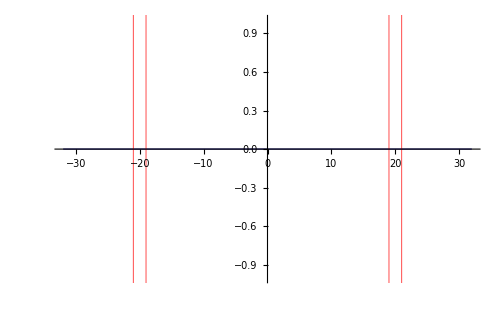

```mathematica
Redlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red}},None},ImageSize->500]
```

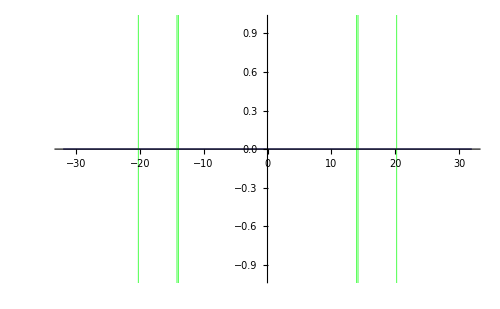

```mathematica
Greenlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

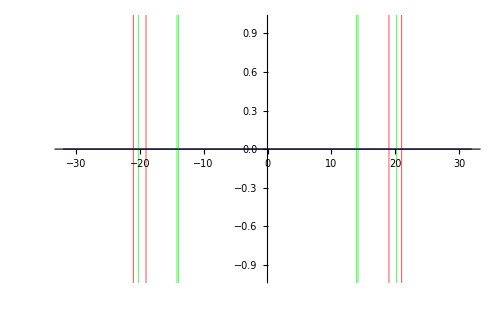

```mathematica
Alllines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red},{δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

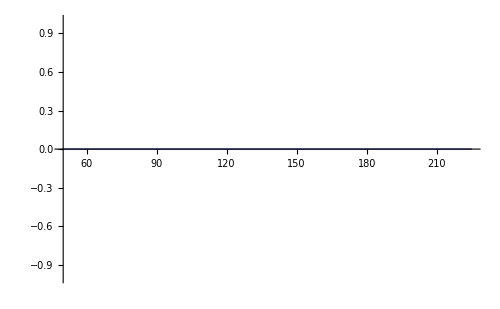

```mathematica
Alllines1=Plot[0,{x,50,225},GridLines->{{ {eig1,Red},{eig2,Red},{eig3,Red},{eig4,Red},{eig5,Green},{eig6,Green},{eig7,Green},{eig8,Green},{eig9,Green},{eig10,Green},{eig11,Green},{eig12,Green}},None},ImageSize->500]
```

## Deloc 1 eigenvalues eigenvectors

```mathematica
Clear["Global`*"];
```

```mathematica
Nt=3;(* Truncation *)
dim=Nt^2*4;
```

```mathematica
g=0.1;
J=1;
ω0=1000;
ωc=1000;
```

### JC model

### Set operators

```mathematica
temp[x_,y_]:=0;For[i=1,i≤Nt-1,i++,temp[i,i+1]=√i]
a=Array[temp,{Nt,Nt}];Clear[temp];
SuperDagger[a]=Transpose[a];
(*a//MatrixForm
ad//MatrixForm*)

σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
SubPlus[σ]={{0,0},{1,0}};
SubMinus[σ]={{0,1},{0,0}};

IDc[x_]:=IdentityMatrix[Nt^x];
IDa:=IdentityMatrix[2];
IDtot=IdentityMatrix[dim];
a_⊗b_ := KroneckerProduct[a,b];
a_⊗b_⊗c_ := KroneckerProduct[KroneckerProduct[a,b],c];
a_⊗b_⊗c_⊗d_ := KroneckerProduct[KroneckerProduct[KroneckerProduct[a,b],c],d];
```

### Hamiltonian for two cavities and no atom

```mathematica
c[1]=a⊗IDc[1]⊗IDa⊗IDa;
c[2]=IDc[1]⊗a⊗IDa⊗IDa;
SuperDagger[c][1]=SuperDagger[a]⊗IDc[1]⊗IDa⊗IDa;
SuperDagger[c][2]=IDc[1]⊗SuperDagger[a]⊗IDa⊗IDa;
n[1]=SuperDagger[a].a⊗IDc[1]⊗IDa⊗IDa;
n[2]=IDc[1]⊗SuperDagger[a].a⊗IDa⊗IDa;
s[1]=IDc[1]⊗IDc[1]⊗SubMinus[σ]⊗IDa;
SuperDagger[s][1]=IDc[1]⊗IDc[1]⊗SubPlus[σ]⊗IDa;
s[2]=IDc[1]⊗IDc[1]⊗IDa⊗SubMinus[σ];
SuperDagger[s][2]=IDc[1]⊗IDc[1]⊗IDa⊗SubPlus[σ];
```

```mathematica
Hfree=ω0 SuperDagger[s][1].s[1]+ω0 SuperDagger[s][2].s[2]+ωc n[1]+ωc n[2];
Hcavinty=-J(SuperDagger[c][1].c[2]+c[1].SuperDagger[c][2]);
Hatomcavity=g(SuperDagger[c][1].s[1]+c[1].SuperDagger[s][1])+g(SuperDagger[c][2].s[2]+c[2].SuperDagger[s][2]);
Htot=Hfree+Hcavinty+Hatomcavity;
```

```mathematica
vac=ReplacePart[ConstantArray[0,{dim}],{1}->1];
```

```mathematica
(*Htot//MatrixForm*)
```

```mathematica
1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
v20=SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20

v20=1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20
```

4000.

2000.

-> Hilber space I use here is not based on {|0>,a^†|0>,(a^†)^2|0>}, but based on {|0>,|1>,|2>}, where |1>=a^†|0> and | 2 >= 1/Sqrt[2](a^†)^2 |0>.

```mathematica
(*s^†[2].vac
s^†[1].vac
s^†[2].s^†[1].vac

c^†[2].vac
c^†[2].s^†[2].vac
c^†[2].s^†[1].vac
c^†[2].s^†[2].s^†[1].vac

c^†[2].c^†[2].vac
c^†[2].c^†[2].s^†[2].vac
c^†[2].c^†[2].s^†[1].vac
c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].vac
c^†[1].s^†[2].vac
c^†[1].s^†[1].vac
c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[2].vac
c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].vac
c^†[1].c^†[1].s^†[2].vac
c^†[1].c^†[1].s^†[1].vac
c^†[1].c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac*)
```

-> The order of basis for two cavities is used as {|00gg>,|00ge>,|00eg>,|00ee>,|01gg>,|01ge>,|01eg>,|01ee>,|02gg>,|02ge>,|02eg>,|02ee>,|10gg>,|10ge>,|10eg>,|10ee>... }.

### Find eigenvalues

```mathematica
{eval,evec}=Eigensystem[Htot];
```

```mathematica
basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","|01ee>",
"|02gg>","|02ge>","|02eg>","|02ee>",
"|10gg>","|10ge>","|10eg>","|10ee>",
"|11gg>","|11ge>","|11eg>","|11ee>",
"|12gg>","|12ge>","|12eg>","|12ee>",
"|20gg>","|20ge>","|20eg>","|20ee>",
"|21gg>","|21ge>","|21eg>","|21ee>",
"|22gg>","|22ge>","|22eg>","|22ee>"
};
```

```mathematica
evaltab={};
evectab={};
Do[AppendTo[evaltab,eval[[i]]//FullSimplify],{i,1,10}]
Do[AppendTo[evectab,(evec[[i]]//FullSimplify).basisset],{i,1,10}]
```

```mathematica
evaltab//MatrixForm
evectab//MatrixForm
```

(6000.
5002.01
5000.01
4999.99
4997.99
4002.16
4002.
4001.86
4000.
4000.)

(0.+1. |22ee>
0.-0.705363 |12ee>+0.705363 |21ee>+0.0496298 |22eg>-0.0496298 |22ge>
0.+0.0496298 |12ee>+0.0496298 |21ee>+0.705363 |22eg>+0.705363 |22ge>
0.+0.0496298 |12ee>-0.0496298 |21ee>+0.705363 |22eg>-0.705363 |22ge>
0.-0.705363 |12ee>-0.705363 |21ee>+0.0496298 |22eg>+0.0496298 |22ge>
0.-2.03278×10^-29 |00ee>+1.38338×10^-45 |00eg>-4.60796×10^-49 |00ge>+8.604×10^-23 |01ee>-2.71327×10^-25 |01eg>+2.03283×10^-28 |01ge>-1.38338×10^-44 |01gg>-0.343105 |02ee>-8.77161×10^-22 |02eg>-5.77088×10^-22 |02ge>+1.91863×10^-24 |02gg>-4.54553×10^-20 |10ee>+2.7161×10^-22 |10eg>-1.35668×10^-25 |10ge>+4.59177×10^-41 |10gg>+0.497952 |11ee>+6.20034×10^-19 |11eg>+4.08942×10^-19 |11ge>-2.71628×10^-21 |11gg>+0.363702 |12eg>-0.353388 |12ge>-2.1439×10^-20 |12gg>-0.343105 |20ee>-3.88578×10^-16 |20eg>-3.33067×10^-16 |20ge>-0.353388 |21eg>+0.363702 |21ge>+0.0477255 |22gg>
0.-4.9828×10^-25 |00ee>+1.06842×10^-22 |01ee>+4.74714×10^-22 |01eg>+4.98281×10^-24 |01ge>-0.0249688 |02ee>-6.12271×10^-22 |02eg>-9.37093×10^-22 |02ge>-3.35674×10^-21 |02gg>-7.35108×10^-20 |10ee>+4.69225×10^-22 |10eg>+2.37372×10^-22 |10ge>+1.32272×10^-12 |11ee>+4.2413×10^-19 |11eg>+6.60886×10^-19 |11ge>-4.69306×10^-21 |11gg>-0.499376 |12eg>-0.5 |12ge>-1.30171×10^-19 |12gg>+0.0249688 |20ee>-2.498×10^-16 |20eg>-4.44089×10^-16 |20ge>+5.55112×10^-17 |20gg>+0.5 |21eg>+0.499376 |21ge>+4.92043×10^-17 |21gg>+7.53766×10^-14 |22gg>
0.-6.30491×10^-25 |00ee>+7.16222×10^-23 |01ee>+6.12149×10^-22 |01eg>+6.30492×10^-24 |01ge>+0.363702 |02ee>+1.77793×10^-22 |02eg>-7.66411×10^-22 |02ge>-4.32855×10^-21 |02gg>-5.9887×10^-20 |10ee>+4.11534×10^-22 |10eg>+3.06093×10^-22 |10ge>-0.502027 |11ee>-1.43026×10^-19 |11eg>+5.38944×10^-19 |11ge>-4.11624×10^-21 |11gg>+0.343105 |12eg>-0.350167 |12ge>-1.34043×10^-19 |12gg>+0.363702 |20ee>+8.32667×10^-17 |20eg>-3.88578×10^-16 |20ge>-0.350167 |21eg>+0.343105 |21ge>+5.55112×10^-17 |21gg>+0.0522927 |22gg>
0.+1.98523×10^-23 |00ee>+2.76474×10^-29 |00eg>-9.22988×10^-33 |00ge>+3.1225×10^-17 |01ee>-6.52215×10^-20 |01eg>-2.64698×10^-22 |01ge>-2.76475×10^-28 |01gg>-0.706225 |02ee>+6.26452×10^-16 |02eg>-1.63281×10^-16 |02ge>+4.06576×10^-19 |02gg>+2.97885×10^-17 |10ee>-3.64563×10^-18 |10eg>-2.15993×10^-20 |10ge>+8.27181×10^-25 |10gg>+2.88352×10^-7 |11ee>+4.47559×10^-16 |11eg>-5.55112×10^-16 |11ge>+7.63278×10^-17 |11gg>+0.0353112 |12eg>+4.07791×10^-6 |12ge>+2.46948×10^-17 |12gg>+0.706225 |20ee>+4.68057×10^-16 |20eg>-5.97724×10^-16 |20ge>-6.23111×10^-17 |20gg>+4.07791×10^-6 |21eg>-0.0353112 |21ge>-2.43945×10^-19 |21gg>+0.000057382 |22gg>
0.-9.84498×10^-28 |00ee>-1.9515×10^-33 |00eg>-1.59665×10^-36 |00ge>-1.74701×10^-21 |01ee>+3.77401×10^-24 |01eg>+1.37325×10^-26 |01ge>+1.95151×10^-32 |01gg>+0.0000407292 |02ee>-2.59536×10^-20 |02eg>+8.65562×10^-21 |02ge>-2.39882×10^-23 |02gg>-1.36154×10^-21 |10ee>+3.86707×10^-22 |10eg>+1.39587×10^-24 |10ge>-5.04871×10^-29 |10gg>+0.00499987 |11ee>-1.24556×10^-18 |11eg>+4.74338×10^-20 |11ge>-6.35275×10^-21 |11gg>-2.03646×10^-6 |12eg>+0.0707089 |12ge>+2.97668×10^-19 |12gg>-0.0000407292 |20ee>+7.77156×10^-16 |20eg>-1.2855×10^-20 |20ge>+0.0707089 |21eg>+2.03646×10^-6 |21ge>-1.11022×10^-16 |21gg>+0.994975 |22gg>)

### Find eigenvalues of newHtot

```mathematica
(*basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","8",
"|02gg>","10","11","12",
"|10gg>","|10ge>","|10eg>","16",
"|11gg>","18","19","20",
"21","22","23","24",
"|20gg>","26","27","28",
"29","30","31","32",
"33","34","35","36"
};*)
newbasisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>",
"|02gg>",
"|10gg>","|10ge>","|10eg>",
"|11gg>",
"|20gg>"
};
```

```mathematica
newHtot=Drop[Drop[Drop[Drop[Drop[Htot,{8,8},{8,8}],{9,11},{9,11}],{12,12},{12,12}],{13,19},{13,19}],{14,24},{14,24}];
(*newHtot//MatrixForm*)
(*newHtot.newbasisset//MatrixForm*)
```

```mathematica
newHtot//MatrixForm
newbasisset//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1000. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1000. | 0. | 0. | 0. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 2000. | 0. | 0. | 0.1 | 0. | 0. | 0.1 | 0. | 0. | 0.
0. | 0.1 | 0. | 0. | 1000. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 2000. | 0. | 0.141421 | 0. | -1. | 0. | 0. | 0.
0. | 0. | 0. | 0.1 | 0. | 0. | 2000. | 0. | 0. | 0. | -1. | 0.1 | 0.
0. | 0. | 0. | 0. | 0. | 0.141421 | 0. | 2000. | 0. | 0. | 0. | -1.41421 | 0.
0. | 0. | 0.1 | 0. | -1. | 0. | 0. | 0. | 1000. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.1 | 0. | -1. | 0. | 0. | 0. | 2000. | 0. | 0.1 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 2000. | 0. | 0.141421
0. | 0. | 0. | 0. | 0. | 0. | 0.1 | -1.41421 | 0. | 0.1 | 0. | 2000. | -1.41421
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.141421 | -1.41421 | 2000.)

(|00gg>
|00ge>
|00eg>
|00ee>
|01gg>
|01ge>
|01eg>
|02gg>
|10gg>
|10ge>
|10eg>
|11gg>
|20gg>)

```mathematica
H=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ω0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ω0, 0, 0, 0, 0, 0, g, 0, 0, 0, 0}, {0, 0, 0, 2 ω0, 0, 0, g, 0, 0, g, 0, 0, 0}, {0, g, 0, 0, ωc, 0, 0, 0, -J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ω0+ωc, 0, √2 g, 0, -J, 0, 0, 0}, {0, 0, 0, g, 0, 0, ω0+ωc, 0, 0, 0, -J, g, 0}, {0, 0, 0, 0, 0, √2 g, 0, 2 ωc, 0, 0, 0, -√2 J, 0}, {0, 0, g, 0, -J, 0, 0, 0, ωc, 0, 0, 0, 0}, {0, 0, 0, g, 0, -J, 0, 0, 0, ω0+ωc, 0, g, 0}, {0, 0, 0, 0, 0, 0, -J, 0, 0, 0, ω0+ωc, 0, √2 g}, {0, 0, 0, 0, 0, 0, g, -√2 J, 0, g, 0, 2 ωc, -√2 J}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, √2 g, -√2 J, 2 ωc}})
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1000,0,0,0.1,0,0,0,0,0,0,0,0},{0,0,1000,0,0,0,0,0,0.1,0,0,0,0},{0,0,0,2000,0,0,0.1,0,0,0.1,0,0,0},{0,0.1,0,0,1000,0,0,0,-1,0,0,0,0},{0,0,0,0,0,2000,0,0.141421,0,-1,0,0,0},{0,0,0,0.1,0,0,2000,0,0,0,-1,0.1,0},{0,0,0,0,0,0.141421,0,2000,0,0,0,-√2,0},{0,0,0.1,0,-1,0,0,0,1000,0,0,0,0},{0,0,0,0.1,0,-1,0,0,0,2000,0,0.1,0},{0,0,0,0,0,0,-1,0,0,0,2000,0,0.141421},{0,0,0,0,0,0,0.1,-√2,0,0.1,0,2000,-√2},{0,0,0,0,0,0,0,0,0,0,0.141421,-√2,2000}}

```mathematica
{neweval,newevec}=Eigensystem[newHtot];
```

```mathematica
newevec=Round[newevec,0.01];
newevaltab={};
newevectab={};
Do[AppendTo[newevaltab,neweval[[i]]//Simplify],{i,1,13}];
Do[AppendTo[newevectab,(Round[Normalize[newevec[[i]]],0.01]//Simplify//Chop//N).newbasisset],{i,1,13}]
```

```mathematica
newevaltab//MatrixForm//N
newevectab//MatrixForm
```

(2002.02
2001.01
2000.99
2000.
2000.
1999.01
1998.99
1997.98
1001.01
1000.01
999.99
998.99
0.)

(0.-0.01 |00ee>-0.07 |01eg>+0.07 |01ge>+0.5 |02gg>+0.07 |10eg>-0.07 |10ge>-0.7 |11gg>+0.5 |20gg>
0.+0.5 |01eg>+0.5 |01ge>+0.07 |02gg>-0.5 |10eg>-0.5 |10ge>-0.07 |20gg>
0.-0.1 |00ee>-0.5 |01eg>+0.49 |01ge>-0.07 |02gg>+0.49 |10eg>-0.5 |10ge>+0.1 |11gg>-0.07 |20gg>
0.-0.06 |00ee>+0.1 |01eg>-0.01 |01ge>-0.7 |02gg>-0.01 |10eg>-0.1 |10ge>+0.7 |20gg>
0.-0.99 |00ee>-0.01 |01eg>-0.1 |01ge>+0.05 |02gg>-0.1 |10eg>+0.01 |10ge>-0.01 |11gg>-0.05 |20gg>
0.+0.1 |00ee>-0.5 |01eg>-0.49 |01ge>-0.07 |02gg>-0.49 |10eg>-0.5 |10ge>-0.1 |11gg>-0.07 |20gg>
0.+0.5 |01eg>-0.5 |01ge>+0.07 |02gg>+0.5 |10eg>-0.5 |10ge>-0.07 |20gg>
0.-0.01 |00ee>+0.07 |01eg>+0.07 |01ge>-0.5 |02gg>+0.07 |10eg>+0.07 |10ge>-0.7 |11gg>-0.5 |20gg>
0.+0.07 |00eg>-0.07 |00ge>-0.7 |01gg>+0.7 |10gg>
0.+0.7 |00eg>+0.7 |00ge>+0.07 |01gg>+0.07 |10gg>
0.+0.7 |00eg>-0.7 |00ge>+0.07 |01gg>-0.07 |10gg>
0.+0.07 |00eg>+0.07 |00ge>-0.7 |01gg>-0.7 |10gg>
0.+1. |00gg>)

```mathematica
eig1=newevaltab[[12]]//N
eig2=newevaltab[[11]]//N
eig3=newevaltab[[10]]//N
eig4=newevaltab[[9]]//N
eig5=newevaltab[[8]]//N
eig6=newevaltab[[7]]//N
eig7=newevaltab[[6]]//N
eig8=newevaltab[[5]]//N
eig9=newevaltab[[4]]//N
eig10=newevaltab[[3]]//N
eig11=newevaltab[[2]]//N
eig12=newevaltab[[1]]//N
```

998.99

999.99

1000.01

1001.01

1997.98

1998.99

1999.01

2000.

2000.

2000.99

2001.01

2002.02

```mathematica
δ1= 2eig1-2ωc;
δ2= 2eig2-2ωc;
δ3= 2eig3-2ωc;
δ4= 2eig4-2ωc;
δ5= eig5-2ωc;
δ6=eig6-2ωc;
δ7= eig7-2ωc;
δ8= eig8-2ωc;
δ9= eig9-2ωc;
δ10= eig10-2ωc;
δ11= eig11-2ωc;
δ12= eig12-2ωc;
```

```mathematica
mmin=-32;
mmax=32;
```

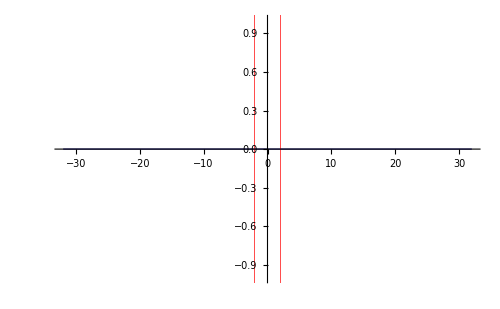

```mathematica
Redlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red}},None},ImageSize->500]
```

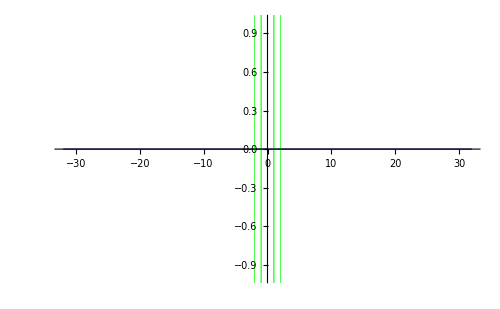

```mathematica
Greenlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

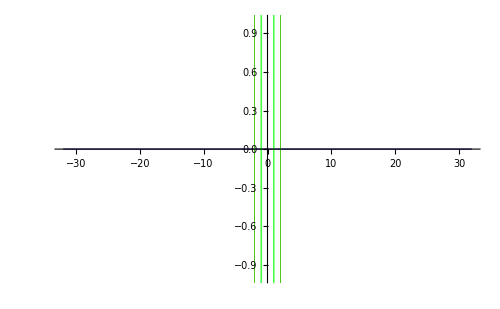

```mathematica
Alllines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red},{δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

```mathematica
Alllines1=Plot[0,{x,50,225},GridLines->{{ {eig1,Red},{eig2,Red},{eig3,Red},{eig4,Red},{eig5,Green},{eig6,Green},{eig7,Green},{eig8,Green},{eig9,Green},{eig10,Green},{eig11,Green},{eig12,Green}},None},ImageSize->500]
```

-Graphics-

```mathematica
{{eig12=2002.0197092892317}, {eig11=2001.009950493836}, {eig10=2000.990340540921}, {eig9=1999.9999999999998}, {eig8=1999.9999999999993}, {eig7=1999.009659459079}, {eig6=1998.9900495061643}, {eig5=1997.980290710769}, {eig4=1001.0099019513582}, {eig3=1000.0099019513602}, {eig2=999.9900980486416}, {eig1=998.9900980486397}}
```

## Loc 1 eigenvalues eigenvectors

```mathematica
Clear["Global`*"];
```

```mathematica
Nt=3;(* Truncation *)
dim=Nt^2*4;
```

```mathematica
g=10;
J=1;
ω0=1000;
ωc=1000;
```

### JC model

### Set operators

```mathematica
temp[x_,y_]:=0;For[i=1,i≤Nt-1,i++,temp[i,i+1]=√i]
a=Array[temp,{Nt,Nt}];Clear[temp];
SuperDagger[a]=Transpose[a];
(*a//MatrixForm
ad//MatrixForm*)

σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
SubPlus[σ]={{0,0},{1,0}};
SubMinus[σ]={{0,1},{0,0}};

IDc[x_]:=IdentityMatrix[Nt^x];
IDa:=IdentityMatrix[2];
IDtot=IdentityMatrix[dim];
a_⊗b_ := KroneckerProduct[a,b];
a_⊗b_⊗c_ := KroneckerProduct[KroneckerProduct[a,b],c];
a_⊗b_⊗c_⊗d_ := KroneckerProduct[KroneckerProduct[KroneckerProduct[a,b],c],d];
```

### Hamiltonian for two cavities and no atom

```mathematica
c[1]=a⊗IDc[1]⊗IDa⊗IDa;
c[2]=IDc[1]⊗a⊗IDa⊗IDa;
SuperDagger[c][1]=SuperDagger[a]⊗IDc[1]⊗IDa⊗IDa;
SuperDagger[c][2]=IDc[1]⊗SuperDagger[a]⊗IDa⊗IDa;
n[1]=SuperDagger[a].a⊗IDc[1]⊗IDa⊗IDa;
n[2]=IDc[1]⊗SuperDagger[a].a⊗IDa⊗IDa;
s[1]=IDc[1]⊗IDc[1]⊗SubMinus[σ]⊗IDa;
SuperDagger[s][1]=IDc[1]⊗IDc[1]⊗SubPlus[σ]⊗IDa;
s[2]=IDc[1]⊗IDc[1]⊗IDa⊗SubMinus[σ];
SuperDagger[s][2]=IDc[1]⊗IDc[1]⊗IDa⊗SubPlus[σ];
```

```mathematica
Hfree=ω0 SuperDagger[s][1].s[1]+ω0 SuperDagger[s][2].s[2]+ωc n[1]+ωc n[2];
Hcavinty=-J(SuperDagger[c][1].c[2]+c[1].SuperDagger[c][2]);
Hatomcavity=g(SuperDagger[c][1].s[1]+c[1].SuperDagger[s][1])+g(SuperDagger[c][2].s[2]+c[2].SuperDagger[s][2]);
Htot=Hfree+Hcavinty+Hatomcavity;
```

```mathematica
vac=ReplacePart[ConstantArray[0,{dim}],{1}->1];
```

```mathematica
(*Htot//MatrixForm*)
```

```mathematica
1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
v20=SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20

v20=1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20
```

4000

2000

-> Hilber space I use here is not based on {|0>,a^†|0>,(a^†)^2|0>}, but based on {|0>,|1>,|2>}, where |1>=a^†|0> and | 2 >= 1/Sqrt[2](a^†)^2 |0>.

```mathematica
(*s^†[2].vac
s^†[1].vac
s^†[2].s^†[1].vac

c^†[2].vac
c^†[2].s^†[2].vac
c^†[2].s^†[1].vac
c^†[2].s^†[2].s^†[1].vac

c^†[2].c^†[2].vac
c^†[2].c^†[2].s^†[2].vac
c^†[2].c^†[2].s^†[1].vac
c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].vac
c^†[1].s^†[2].vac
c^†[1].s^†[1].vac
c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[2].vac
c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].vac
c^†[1].c^†[1].s^†[2].vac
c^†[1].c^†[1].s^†[1].vac
c^†[1].c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac*)
```

-> The order of basis for two cavities is used as {|00gg>,|00ge>,|00eg>,|00ee>,|01gg>,|01ge>,|01eg>,|01ee>,|02gg>,|02ge>,|02eg>,|02ee>,|10gg>,|10ge>,|10eg>,|10ee>... }.

### Find eigenvalues

```mathematica
{eval,evec}=Eigensystem[Htot];
```

```mathematica
basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","|01ee>",
"|02gg>","|02ge>","|02eg>","|02ee>",
"|10gg>","|10ge>","|10eg>","|10ee>",
"|11gg>","|11ge>","|11eg>","|11ee>",
"|12gg>","|12ge>","|12eg>","|12ee>",
"|20gg>","|20ge>","|20eg>","|20ee>",
"|21gg>","|21ge>","|21eg>","|21ee>",
"|22gg>","|22ge>","|22eg>","|22ee>"
};
```

```mathematica
evaltab={};
evectab={};
Do[AppendTo[evaltab,eval[[i]]//FullSimplify],{i,1,10}]
Do[AppendTo[evectab,(evec[[i]]//FullSimplify).basisset],{i,1,10}]
```

```mathematica
evaltab//MatrixForm
evectab//MatrixForm
```

(6000
5001+√201
4999+√201
5001-√201
4999-√201
4000+√(454+10 √1261)
2 (2000+√26)
4000+√(454-10 √1261)
4000
4000)

(|22ee>
-1/10 √(101+√201) |12ee>+1/20 (√2+√402) |21ee>+|22eg>-|22ge>
((-1+√201) |12ee>)/(10 √2)+((-1+√201) |21ee>)/(10 √2)+|22eg>+|22ge>
((-1+√201) |12ee>)/(10 √2)+1/20 (√2-√402) |21ee>+|22eg>-|22ge>
-1/10 √(101+√201) |12ee>-1/10 √(101+√201) |21ee>+|22eg>+|22ge>
1/60 (25+√1261) |11ee>+1/20 √(227+5 √1261) |12eg>-(19 |12ge>)/(10 √(2311/13+5 √1261))-(19 |21eg>)/(10 √(2311/13+5 √1261))+1/20 √(227+5 √1261) |21ge>+|22gg>+|02ee> Root[45009-6148600 #1^2+360000 #1^4&,2]+|20ee> Root[45009-6148600 #1^2+360000 #1^4&,2]
-(5 |02ee>)/(√26)-(|12eg>)/(√26)-|12ge>+(5 |20ee>)/(√26)+|21eg>+(|21ge>)/(√26)
1/60 √(30743+865 √1261) |02ee>+1/60 (25-√1261) |11ee>+1/20 √(227-5 √1261) |12eg>+((169+5 √1261) |12ge>)/(60 √2)+1/60 √(30743+865 √1261) |20ee>+((169+5 √1261) |21eg>)/(60 √2)+1/20 √(227-5 √1261) |21ge>+|22gg>
-(50 |11ee>)/49-(5 √2 |12ge>)/49-(5 √2 |21eg>)/49+|22gg>
(|02ee>)/5-|12eg>-(|20ee>)/5+|21ge>)

### Find eigenvalues of newHtot

```mathematica
(*basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","8",
"|02gg>","10","11","12",
"|10gg>","|10ge>","|10eg>","16",
"|11gg>","18","19","20",
"21","22","23","24",
"|20gg>","26","27","28",
"29","30","31","32",
"33","34","35","36"
};*)
newbasisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>",
"|02gg>",
"|10gg>","|10ge>","|10eg>",
"|11gg>",
"|20gg>"
};
```

```mathematica
newHtot=Drop[Drop[Drop[Drop[Drop[Htot,{8,8},{8,8}],{9,11},{9,11}],{12,12},{12,12}],{13,19},{13,19}],{14,24},{14,24}];
(*newHtot//MatrixForm*)
(*newHtot.newbasisset//MatrixForm*)
```

```mathematica
newHtot//MatrixForm
newbasisset//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1000 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1000 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2000 | 0 | 0 | 10 | 0 | 0 | 10 | 0 | 0 | 0
0 | 10 | 0 | 0 | 1000 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2000 | 0 | 10 √2 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 10 | 0 | 0 | 2000 | 0 | 0 | 0 | -1 | 10 | 0
0 | 0 | 0 | 0 | 0 | 10 √2 | 0 | 2000 | 0 | 0 | 0 | -√2 | 0
0 | 0 | 10 | 0 | -1 | 0 | 0 | 0 | 1000 | 0 | 0 | 0 | 0
0 | 0 | 0 | 10 | 0 | -1 | 0 | 0 | 0 | 2000 | 0 | 10 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2000 | 0 | 10 √2
0 | 0 | 0 | 0 | 0 | 0 | 10 | -√2 | 0 | 10 | 0 | 2000 | -√2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 √2 | -√2 | 2000)

(|00gg>
|00ge>
|00eg>
|00ee>
|01gg>
|01ge>
|01eg>
|02gg>
|10gg>
|10ge>
|10eg>
|11gg>
|20gg>)

```mathematica
H=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ω0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ω0, 0, 0, 0, 0, 0, g, 0, 0, 0, 0}, {0, 0, 0, 2 ω0, 0, 0, g, 0, 0, g, 0, 0, 0}, {0, g, 0, 0, ωc, 0, 0, 0, -J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ω0+ωc, 0, √2 g, 0, -J, 0, 0, 0}, {0, 0, 0, g, 0, 0, ω0+ωc, 0, 0, 0, -J, g, 0}, {0, 0, 0, 0, 0, √2 g, 0, 2 ωc, 0, 0, 0, -√2 J, 0}, {0, 0, g, 0, -J, 0, 0, 0, ωc, 0, 0, 0, 0}, {0, 0, 0, g, 0, -J, 0, 0, 0, ω0+ωc, 0, g, 0}, {0, 0, 0, 0, 0, 0, -J, 0, 0, 0, ω0+ωc, 0, √2 g}, {0, 0, 0, 0, 0, 0, g, -√2 J, 0, g, 0, 2 ωc, -√2 J}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, √2 g, -√2 J, 2 ωc}})
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1000,0,0,10,0,0,0,0,0,0,0,0},{0,0,1000,0,0,0,0,0,10,0,0,0,0},{0,0,0,2000,0,0,10,0,0,10,0,0,0},{0,10,0,0,1000,0,0,0,-1,0,0,0,0},{0,0,0,0,0,2000,0,10 √2,0,-1,0,0,0},{0,0,0,10,0,0,2000,0,0,0,-1,10,0},{0,0,0,0,0,10 √2,0,2000,0,0,0,-√2,0},{0,0,10,0,-1,0,0,0,1000,0,0,0,0},{0,0,0,10,0,-1,0,0,0,2000,0,10,0},{0,0,0,0,0,0,-1,0,0,0,2000,0,10 √2},{0,0,0,0,0,0,10,-√2,0,10,0,2000,-√2},{0,0,0,0,0,0,0,0,0,0,10 √2,-√2,2000}}

```mathematica
{neweval,newevec}=Eigensystem[newHtot];
```

```mathematica
newevec=Round[newevec,0.01];
newevaltab={};
newevectab={};
Do[AppendTo[newevaltab,neweval[[i]]//Simplify],{i,1,13}];
Do[AppendTo[newevectab,(Round[Normalize[newevec[[i]]],0.01]//Simplify//Chop//N).newbasisset],{i,1,13}]
```

```mathematica
newevaltab//MatrixForm//N
newevectab//MatrixForm
```

(2020.24
2014.18
2013.97
2000.
2000.
1986.03
1985.82
1979.76
1010.51
1009.51
990.488
989.488
0.)

(0.-0.48 |00ee>-0.49 |01eg>+0.09 |01ge>+0.1 |02gg>+0.09 |10eg>-0.49 |10ge>-0.5 |11gg>+0.1 |20gg>
0.-0.03 |01eg>-0.5 |01ge>-0.5 |02gg>+0.5 |10eg>+0.03 |10ge>+0.5 |20gg>
0.+0.15 |00ee>+0.1 |01eg>+0.49 |01ge>+0.49 |02gg>+0.49 |10eg>+0.1 |10ge>+0.04 |11gg>+0.49 |20gg>
0.+0.71 |01eg>-0.05 |02gg>-0.71 |10ge>+0.05 |20gg>
0.-0.7 |00ee>+0.07 |01ge>+0.07 |10eg>+0.71 |11gg>
0.-0.15 |00ee>+0.1 |01eg>-0.49 |01ge>+0.49 |02gg>-0.49 |10eg>+0.1 |10ge>-0.04 |11gg>+0.49 |20gg>
0.-0.03 |01eg>+0.5 |01ge>-0.5 |02gg>-0.5 |10eg>+0.03 |10ge>+0.5 |20gg>
0.+0.48 |00ee>-0.49 |01eg>-0.09 |01ge>+0.1 |02gg>-0.09 |10eg>-0.49 |10ge>+0.5 |11gg>+0.1 |20gg>
0.+0.49 |00eg>-0.49 |00ge>-0.51 |01gg>+0.51 |10gg>
0.+0.51 |00eg>+0.51 |00ge>+0.49 |01gg>+0.49 |10gg>
0.-0.51 |00eg>+0.51 |00ge>-0.49 |01gg>+0.49 |10gg>
0.-0.49 |00eg>-0.49 |00ge>+0.51 |01gg>+0.51 |10gg>
0.+1. |00gg>)

```mathematica
eig1=newevaltab[[12]]//N
eig2=newevaltab[[11]]//N
eig3=newevaltab[[10]]//N
eig4=newevaltab[[9]]//N
eig5=newevaltab[[8]]//N
eig6=newevaltab[[7]]//N
eig7=newevaltab[[6]]//N
eig8=newevaltab[[5]]//N
eig9=newevaltab[[4]]//N
eig10=newevaltab[[3]]//N
eig11=newevaltab[[2]]//N
eig12=newevaltab[[1]]//N
```

989.488

990.488

1009.51

1010.51

1979.76

1985.82

1986.03

2000.

2000.

2013.97

2014.18

2020.24

```mathematica
δ1= 2eig1-2ωc;
δ2= 2eig2-2ωc;
δ3= 2eig3-2ωc;
δ4= 2eig4-2ωc;
δ5= eig5-2ωc;
δ6=eig6-2ωc;
δ7= eig7-2ωc;
δ8= eig8-2ωc;
δ9= eig9-2ωc;
δ10= eig10-2ωc;
δ11= eig11-2ωc;
δ12= eig12-2ωc;
```

```mathematica
mmin=-32;
mmax=32;
```

```mathematica
Redlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red}},None},ImageSize->500]
```

-Graphics-

```mathematica
Greenlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

-Graphics-

```mathematica
Alllines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red},{δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

-Graphics-

```mathematica
Alllines1=Plot[0,{x,50,225},GridLines->{{ {eig1,Red},{eig2,Red},{eig3,Red},{eig4,Red},{eig5,Green},{eig6,Green},{eig7,Green},{eig8,Green},{eig9,Green},{eig10,Green},{eig11,Green},{eig12,Green}},None},ImageSize->500]
```

-Graphics-

```mathematica
{{eig12=2020.2422464937479}, {eig11=2014.1774468787578}, {eig10=2013.9732407438773}, {eig9=2000.}, {eig8=2000.}, {eig7=1986.0267592561227}, {eig6=1985.8225531212422}, {eig5=1979.7577535062521}, {eig4=1010.5124921972504}, {eig3=1009.5124921972504}, {eig2=990.4875078027496}, {eig1=989.4875078027496}}
```

{2020.24,2014.18,2013.97,2000.,2000.,1986.03,1985.82,1979.76,1010.51,1009.51,990.488,989.488}

## Atomic 1 eigenvalues eigenvectors

```mathematica
Clear["Global`*"];
```

```mathematica
Nt=3;(* Truncation *)
dim=Nt^2*4;
```

```mathematica
g=0.1;
J=1;
ω0=1000;
ωc=1005;
```

### JC model

### Set operators

```mathematica
temp[x_,y_]:=0;For[i=1,i≤Nt-1,i++,temp[i,i+1]=√i]
a=Array[temp,{Nt,Nt}];Clear[temp];
SuperDagger[a]=Transpose[a];
(*a//MatrixForm
ad//MatrixForm*)

σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
SubPlus[σ]={{0,0},{1,0}};
SubMinus[σ]={{0,1},{0,0}};

IDc[x_]:=IdentityMatrix[Nt^x];
IDa:=IdentityMatrix[2];
IDtot=IdentityMatrix[dim];
a_⊗b_ := KroneckerProduct[a,b];
a_⊗b_⊗c_ := KroneckerProduct[KroneckerProduct[a,b],c];
a_⊗b_⊗c_⊗d_ := KroneckerProduct[KroneckerProduct[KroneckerProduct[a,b],c],d];
```

### Hamiltonian for two cavities and no atom

```mathematica
c[1]=a⊗IDc[1]⊗IDa⊗IDa;
c[2]=IDc[1]⊗a⊗IDa⊗IDa;
SuperDagger[c][1]=SuperDagger[a]⊗IDc[1]⊗IDa⊗IDa;
SuperDagger[c][2]=IDc[1]⊗SuperDagger[a]⊗IDa⊗IDa;
n[1]=SuperDagger[a].a⊗IDc[1]⊗IDa⊗IDa;
n[2]=IDc[1]⊗SuperDagger[a].a⊗IDa⊗IDa;
s[1]=IDc[1]⊗IDc[1]⊗SubMinus[σ]⊗IDa;
SuperDagger[s][1]=IDc[1]⊗IDc[1]⊗SubPlus[σ]⊗IDa;
s[2]=IDc[1]⊗IDc[1]⊗IDa⊗SubMinus[σ];
SuperDagger[s][2]=IDc[1]⊗IDc[1]⊗IDa⊗SubPlus[σ];
```

```mathematica
Hfree=ω0 SuperDagger[s][1].s[1]+ω0 SuperDagger[s][2].s[2]+ωc n[1]+ωc n[2];
Hcavinty=-J(SuperDagger[c][1].c[2]+c[1].SuperDagger[c][2]);
Hatomcavity=g(SuperDagger[c][1].s[1]+c[1].SuperDagger[s][1])+g(SuperDagger[c][2].s[2]+c[2].SuperDagger[s][2]);
Htot=Hfree+Hcavinty+Hatomcavity;
```

```mathematica
vac=ReplacePart[ConstantArray[0,{dim}],{1}->1];
```

```mathematica
(*Htot//MatrixForm*)
```

```mathematica
1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
v20=SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20

v20=1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20
```

4020.

2010.

-> Hilber space I use here is not based on {|0>,a^†|0>,(a^†)^2|0>}, but based on {|0>,|1>,|2>}, where |1>=a^†|0> and | 2 >= 1/Sqrt[2](a^†)^2 |0>.

```mathematica
(*s^†[2].vac
s^†[1].vac
s^†[2].s^†[1].vac

c^†[2].vac
c^†[2].s^†[2].vac
c^†[2].s^†[1].vac
c^†[2].s^†[2].s^†[1].vac

c^†[2].c^†[2].vac
c^†[2].c^†[2].s^†[2].vac
c^†[2].c^†[2].s^†[1].vac
c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].vac
c^†[1].s^†[2].vac
c^†[1].s^†[1].vac
c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[2].vac
c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].vac
c^†[1].c^†[1].s^†[2].vac
c^†[1].c^†[1].s^†[1].vac
c^†[1].c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac*)
```

-> The order of basis for two cavities is used as {|00gg>,|00ge>,|00eg>,|00ee>,|01gg>,|01ge>,|01eg>,|01ee>,|02gg>,|02ge>,|02eg>,|02ee>,|10gg>,|10ge>,|10eg>,|10ee>... }.

### Find eigenvalues

```mathematica
{eval,evec}=Eigensystem[Htot];
```

```mathematica
basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","|01ee>",
"|02gg>","|02ge>","|02eg>","|02ee>",
"|10gg>","|10ge>","|10eg>","|10ee>",
"|11gg>","|11ge>","|11eg>","|11ee>",
"|12gg>","|12ge>","|12eg>","|12ee>",
"|20gg>","|20ge>","|20eg>","|20ee>",
"|21gg>","|21ge>","|21eg>","|21ee>",
"|22gg>","|22ge>","|22eg>","|22ee>"
};
```

```mathematica
evaltab={};
evectab={};
Do[AppendTo[evaltab,eval[[i]]//FullSimplify],{i,1,10}]
Do[AppendTo[evectab,(evec[[i]]//FullSimplify).basisset],{i,1,10}]
```

```mathematica
evaltab//MatrixForm
evectab//MatrixForm
```

(6020.
5020.01
5020.
5016.99
5013.
4020.01
4017.
4017.
4013.
4013.)

(0.+1. |22ee>
0.-0.0332229 |12ee>+0.0332229 |21ee>+0.706326 |22eg>-0.706326 |22ge>
0.+0.014277 |12ee>+0.014277 |21ee>+0.706963 |22eg>+0.706963 |22ge>
0.-0.706326 |12ee>+0.706326 |21ee>-0.0332229 |22eg>+0.0332229 |22ge>
0.-0.706963 |12ee>-0.706963 |21ee>+0.014277 |22eg>+0.014277 |22ge>
0.+5.37608×10^-30 |00ee>+3.52616×10^-46 |00eg>-1.16889×10^-49 |00ge>-5.9453×10^-25 |01ee>+7.23622×10^-26 |01eg>-5.40371×10^-29 |01ge>-3.53006×10^-45 |01gg>-0.000279178 |02ee>+4.65645×10^-23 |02eg>+2.4437×10^-24 |02ge>-5.13714×10^-25 |02gg>+4.35617×10^-22 |10ee>-7.27968×10^-23 |10eg>+3.6235×10^-26 |10ge>+0.00102768 |11ee>+2.18441×10^-20 |11eg>-1.74569×10^-21 |11ge>+7.30138×10^-22 |11gg>+0.0335768 |12eg>-0.0134108 |12ge>+7.83076×10^-19 |12gg>-0.000279178 |20ee>-2.77556×10^-17 |20eg>-1.73472×10^-18 |20ge>-8.67362×10^-19 |20gg>-0.0134108 |21eg>+0.0335768 |21ge>-4.44089×10^-16 |21gg>+0.998691 |22gg>
0.-2.20056×10^-25 |00ee>+2.18418×10^-23 |01ee>-3.22456×10^-24 |01eg>+2.02573×10^-24 |01ge>+0.00714304 |02ee>+5.85657×10^-23 |02eg>-1.48284×10^-22 |02ge>+9.4456×10^-23 |02gg>-1.10464×10^-20 |10ee>+1.24191×10^-20 |10eg>-3.33315×10^-24 |10ge>+3.72966×10^-12 |11ee>+2.42403×10^-20 |11eg>+1.05675×10^-19 |11ge>-1.24463×10^-19 |11gg>+0.499885 |12eg>+0.500064 |12ge>-6.18499×10^-20 |12gg>-0.00714304 |20ee>-2.77556×10^-17 |20ge>+2.22045×10^-16 |20gg>-0.500064 |21eg>-0.499885 |21ge>-9.54098×10^-17 |21gg>-6.97287×10^-12 |22gg>
0.-2.19464×10^-25 |00ee>+2.18033×10^-23 |01ee>-3.2697×10^-24 |01eg>+2.02018×10^-24 |01ge>+0.0122117 |02ee>+6.39925×10^-23 |02eg>-1.4828×10^-22 |02ge>+9.4579×10^-23 |02gg>-1.10099×10^-20 |10ee>+1.2439×10^-20 |10eg>-3.35103×10^-24 |10ge>-0.0250905 |11ee>+2.72824×10^-20 |11eg>+1.05671×10^-19 |11ge>-1.24663×10^-19 |11gg>-0.498675 |12eg>+0.499755 |12ge>+6.62075×10^-21 |12gg>+0.0122117 |20ee>-9.54098×10^-18 |20eg>-2.77556×10^-17 |20ge>+2.22045×10^-16 |20gg>+0.499755 |21eg>-0.498675 |21ge>-1.21431×10^-16 |21gg>+0.0469861 |22gg>
0.+2.92657×10^-26 |00ee>-4.00927×10^-23 |01ee>-5.33851×10^-24 |01eg>-1.64129×10^-26 |01ge>+0.00978539 |02ee>+6.89678×10^-22 |02eg>+1.79455×10^-22 |02ge>+3.75237×10^-23 |02gg>+2.75059×10^-20 |10ee>+5.20051×10^-21 |10eg>-2.63409×10^-24 |10ge>-9.40395×10^-38 |10gg>-0.0561291 |11ee>+1.16521×10^-19 |11eg>-1.26176×10^-19 |11ge>-5.31342×10^-20 |11gg>-0.498302 |12eg>-0.499821 |12ge>-7.00165×10^-19 |12gg>+0.00978539 |20ee>-4.51028×10^-17 |20eg>+1.52656×10^-16 |20ge>+7.63278×10^-17 |20gg>-0.499821 |21eg>-0.498302 |21ge>-6.245×10^-16 |21gg>+0.0201463 |22gg>
0.+2.92112×10^-26 |00ee>-3.97381×10^-23 |01ee>-5.2825×10^-24 |01eg>-1.64141×10^-26 |01ge>-0.0166459 |02ee>+7.53251×10^-22 |02eg>+1.78723×10^-22 |02ge>+3.71285×10^-23 |02gg>+2.7181×10^-20 |10ee>+5.14442×10^-21 |10eg>-2.60624×10^-24 |10ge>-1.41059×10^-37 |10gg>+9.11828×10^-12 |11ee>+1.17371×10^-19 |11eg>-1.25549×10^-19 |11ge>-5.25744×10^-20 |11gg>+0.50007 |12eg>-0.499653 |12ge>-1.05108×10^-18 |12gg>+0.0166459 |20ee>-3.64292×10^-17 |20eg>+1.94289×10^-16 |20ge>+1.11022×10^-16 |20gg>+0.499653 |21eg>-0.50007 |21ge>-6.2797×10^-16 |21gg>-3.29881×10^-12 |22gg>)

### Find eigenvalues of newHtot

```mathematica
(*basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","8",
"|02gg>","10","11","12",
"|10gg>","|10ge>","|10eg>","16",
"|11gg>","18","19","20",
"21","22","23","24",
"|20gg>","26","27","28",
"29","30","31","32",
"33","34","35","36"
};*)
newbasisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>",
"|02gg>",
"|10gg>","|10ge>","|10eg>",
"|11gg>",
"|20gg>"
};
```

```mathematica
newHtot=Drop[Drop[Drop[Drop[Drop[Htot,{8,8},{8,8}],{9,11},{9,11}],{12,12},{12,12}],{13,19},{13,19}],{14,24},{14,24}];
(*newHtot//MatrixForm*)
(*newHtot.newbasisset//MatrixForm*)
```

```mathematica
newHtot//MatrixForm
newbasisset//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1000. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1000. | 0. | 0. | 0. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 2000. | 0. | 0. | 0.1 | 0. | 0. | 0.1 | 0. | 0. | 0.
0. | 0.1 | 0. | 0. | 1005. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 2005. | 0. | 0.141421 | 0. | -1. | 0. | 0. | 0.
0. | 0. | 0. | 0.1 | 0. | 0. | 2005. | 0. | 0. | 0. | -1. | 0.1 | 0.
0. | 0. | 0. | 0. | 0. | 0.141421 | 0. | 2010. | 0. | 0. | 0. | -1.41421 | 0.
0. | 0. | 0.1 | 0. | -1. | 0. | 0. | 0. | 1005. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.1 | 0. | -1. | 0. | 0. | 0. | 2005. | 0. | 0.1 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 2005. | 0. | 0.141421
0. | 0. | 0. | 0. | 0. | 0. | 0.1 | -1.41421 | 0. | 0.1 | 0. | 2010. | -1.41421
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.141421 | -1.41421 | 2010.)

(|00gg>
|00ge>
|00eg>
|00ee>
|01gg>
|01ge>
|01eg>
|02gg>
|10gg>
|10ge>
|10eg>
|11gg>
|20gg>)

```mathematica
H=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ω0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ω0, 0, 0, 0, 0, 0, g, 0, 0, 0, 0}, {0, 0, 0, 2 ω0, 0, 0, g, 0, 0, g, 0, 0, 0}, {0, g, 0, 0, ωc, 0, 0, 0, -J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ω0+ωc, 0, √2 g, 0, -J, 0, 0, 0}, {0, 0, 0, g, 0, 0, ω0+ωc, 0, 0, 0, -J, g, 0}, {0, 0, 0, 0, 0, √2 g, 0, 2 ωc, 0, 0, 0, -√2 J, 0}, {0, 0, g, 0, -J, 0, 0, 0, ωc, 0, 0, 0, 0}, {0, 0, 0, g, 0, -J, 0, 0, 0, ω0+ωc, 0, g, 0}, {0, 0, 0, 0, 0, 0, -J, 0, 0, 0, ω0+ωc, 0, √2 g}, {0, 0, 0, 0, 0, 0, g, -√2 J, 0, g, 0, 2 ωc, -√2 J}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, √2 g, -√2 J, 2 ωc}})
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1000,0,0,0.1,0,0,0,0,0,0,0,0},{0,0,1000,0,0,0,0,0,0.1,0,0,0,0},{0,0,0,2000,0,0,0.1,0,0,0.1,0,0,0},{0,0.1,0,0,1005,0,0,0,-1,0,0,0,0},{0,0,0,0,0,2005,0,0.141421,0,-1,0,0,0},{0,0,0,0.1,0,0,2005,0,0,0,-1,0.1,0},{0,0,0,0,0,0.141421,0,2010,0,0,0,-√2,0},{0,0,0.1,0,-1,0,0,0,1005,0,0,0,0},{0,0,0,0.1,0,-1,0,0,0,2005,0,0.1,0},{0,0,0,0,0,0,-1,0,0,0,2005,0,0.141421},{0,0,0,0,0,0,0.1,-√2,0,0.1,0,2010,-√2},{0,0,0,0,0,0,0,0,0,0,0.141421,-√2,2010}}

```mathematica
{neweval,newevec}=Eigensystem[newHtot];
```

```mathematica
newevec=Round[newevec,0.01];
newevaltab={};
newevectab={};
Do[AppendTo[newevaltab,neweval[[i]]//Simplify],{i,1,13}];
Do[AppendTo[newevectab,(Round[Normalize[newevec[[i]]],0.01]//Simplify//Chop//N).newbasisset],{i,1,13}]
```

```mathematica
newevaltab//MatrixForm//N
newevectab//MatrixForm
```

(2012.
2010.
2008.
2006.
2006.
2004.
2004.
2000.
1006.
1004.
999.998
999.998
0.)

(0.-0.01 |01eg>+0.01 |01ge>+0.5 |02gg>+0.01 |10eg>-0.01 |10ge>-0.71 |11gg>+0.5 |20gg>
0.+0.02 |01ge>+0.71 |02gg>-0.02 |10eg>-0.71 |20gg>
0.-0.02 |01eg>-0.02 |01ge>-0.5 |02gg>-0.02 |10eg>-0.02 |10ge>-0.71 |11gg>-0.5 |20gg>
0.+0.02 |00ee>+0.5 |01eg>-0.5 |01ge>+0.01 |02gg>-0.5 |10eg>+0.5 |10ge>-0.02 |11gg>+0.01 |20gg>
0.-0.5 |01eg>-0.5 |01ge>+0.02 |02gg>+0.5 |10eg>+0.5 |10ge>-0.02 |20gg>
0.-0.5 |01eg>+0.5 |01ge>-0.01 |02gg>-0.5 |10eg>+0.5 |10ge>+0.01 |20gg>
0.-0.02 |00ee>-0.5 |01eg>-0.5 |01ge>+0.02 |02gg>-0.5 |10eg>-0.5 |10ge>+0.02 |11gg>+0.02 |20gg>
0.+1. |00ee>-0.02 |01eg>-0.02 |10ge>
0.-0.01 |00eg>+0.01 |00ge>+0.71 |01gg>-0.71 |10gg>
0.-0.02 |00eg>-0.02 |00ge>-0.71 |01gg>-0.71 |10gg>
0.-0.71 |00eg>+0.71 |00ge>-0.01 |01gg>+0.01 |10gg>
0.-0.71 |00eg>-0.71 |00ge>+0.02 |01gg>+0.02 |10gg>
0.+1. |00gg>)

```mathematica
{{eig12=2012.0033319457132}, {eig11=2010.004162911989}, {eig10=2008.0049953227226}, {eig9=2005.998336104832}, {eig8=2005.997504679703}, {eig7=2003.9983324083082}, {eig6=2003.9975015586037}, {eig5=1999.995835068129}, {eig4=1006.0016662039606}, {eig3=1004.0024984394493}, {eig2=999.9983337960398}, {eig1=999.9975015605509}}
```

{2012.,2010.,2008.,2006.,2006.,2004.,2004.,2000.,1006.,1004.,999.998,999.998}

```mathematica
eig1=newevaltab[[12]]//N
eig2=newevaltab[[11]]//N
eig3=newevaltab[[10]]//N
eig4=newevaltab[[9]]//N
eig5=newevaltab[[8]]//N
eig6=newevaltab[[7]]//N
eig7=newevaltab[[6]]//N
eig8=newevaltab[[5]]//N
eig9=newevaltab[[4]]//N
eig10=newevaltab[[3]]//N
eig11=newevaltab[[2]]//N
eig12=newevaltab[[1]]//N
```

999.998

999.998

1004.

1006.

2000.

2004.

2004.

2006.

2006.

2008.

2010.

2012.

```mathematica
δ1= 2eig1-2ωc
δ2= 2eig2-2ωc
δ3= 2eig3-2ωc
δ4= 2eig4-2ωc
δ5= eig5-2ωc
δ6=eig6-2ωc
δ7= eig7-2ωc
δ8= eig8-2ωc
δ9= eig9-2ωc
δ10= eig10-2ωc
δ11= eig11-2ωc
δ12= eig12-2ωc
```

-10.005

-10.0033

-1.995

2.00333

-10.0042

-6.0025

-6.00167

-4.0025

-4.00166

-1.995

0.00416291

2.00333

```mathematica
mmin=-32;
mmax=32;
```

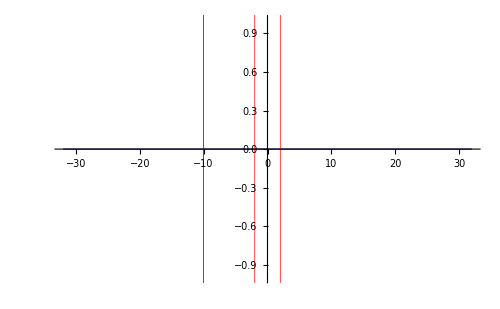

```mathematica
Redlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red}},None},ImageSize->500]
```

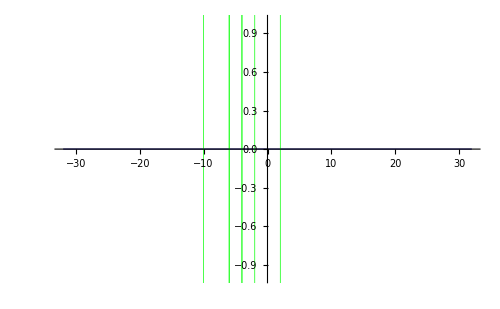

```mathematica
Greenlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

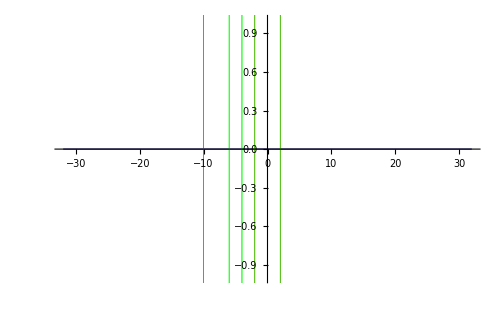

```mathematica
Alllines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red},{δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

```mathematica
Alllines1=Plot[0,{x,50,225},GridLines->{{ {eig1,Red},{eig2,Red},{eig3,Red},{eig4,Red},{eig5,Green},{eig6,Green},{eig7,Green},{eig8,Green},{eig9,Green},{eig10,Green},{eig11,Green},{eig12,Green}},None},ImageSize->500]
```

-Graphics-

## Photonic 1 eigenvalues eigenvectors

```mathematica
Clear["Global`*"];
```

```mathematica
Nt=3;(* Truncation *)
dim=Nt^2*4;
```

```mathematica
g=0.1;
J=1;
ω0=1005;
ωc=1000;
```

### JC model

### Set operators

```mathematica
temp[x_,y_]:=0;For[i=1,i≤Nt-1,i++,temp[i,i+1]=√i]
a=Array[temp,{Nt,Nt}];Clear[temp];
SuperDagger[a]=Transpose[a];
(*a//MatrixForm
ad//MatrixForm*)

σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
SubPlus[σ]={{0,0},{1,0}};
SubMinus[σ]={{0,1},{0,0}};

IDc[x_]:=IdentityMatrix[Nt^x];
IDa:=IdentityMatrix[2];
IDtot=IdentityMatrix[dim];
a_⊗b_ := KroneckerProduct[a,b];
a_⊗b_⊗c_ := KroneckerProduct[KroneckerProduct[a,b],c];
a_⊗b_⊗c_⊗d_ := KroneckerProduct[KroneckerProduct[KroneckerProduct[a,b],c],d];
```

### Hamiltonian for two cavities and no atom

```mathematica
c[1]=a⊗IDc[1]⊗IDa⊗IDa;
c[2]=IDc[1]⊗a⊗IDa⊗IDa;
SuperDagger[c][1]=SuperDagger[a]⊗IDc[1]⊗IDa⊗IDa;
SuperDagger[c][2]=IDc[1]⊗SuperDagger[a]⊗IDa⊗IDa;
n[1]=SuperDagger[a].a⊗IDc[1]⊗IDa⊗IDa;
n[2]=IDc[1]⊗SuperDagger[a].a⊗IDa⊗IDa;
s[1]=IDc[1]⊗IDc[1]⊗SubMinus[σ]⊗IDa;
SuperDagger[s][1]=IDc[1]⊗IDc[1]⊗SubPlus[σ]⊗IDa;
s[2]=IDc[1]⊗IDc[1]⊗IDa⊗SubMinus[σ];
SuperDagger[s][2]=IDc[1]⊗IDc[1]⊗IDa⊗SubPlus[σ];
```

```mathematica
Hfree=ω0 SuperDagger[s][1].s[1]+ω0 SuperDagger[s][2].s[2]+ωc n[1]+ωc n[2];
Hcavinty=-J(SuperDagger[c][1].c[2]+c[1].SuperDagger[c][2]);
Hatomcavity=g(SuperDagger[c][1].s[1]+c[1].SuperDagger[s][1])+g(SuperDagger[c][2].s[2]+c[2].SuperDagger[s][2]);
Htot=Hfree+Hcavinty+Hatomcavity;
```

```mathematica
vac=ReplacePart[ConstantArray[0,{dim}],{1}->1];
```

```mathematica
(*Htot//MatrixForm*)
```

```mathematica
1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
v20=SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20

v20=1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20
```

4000.

2000.

-> Hilber space I use here is not based on {|0>,a^†|0>,(a^†)^2|0>}, but based on {|0>,|1>,|2>}, where |1>=a^†|0> and | 2 >= 1/Sqrt[2](a^†)^2 |0>.

```mathematica
(*s^†[2].vac
s^†[1].vac
s^†[2].s^†[1].vac

c^†[2].vac
c^†[2].s^†[2].vac
c^†[2].s^†[1].vac
c^†[2].s^†[2].s^†[1].vac

c^†[2].c^†[2].vac
c^†[2].c^†[2].s^†[2].vac
c^†[2].c^†[2].s^†[1].vac
c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].vac
c^†[1].s^†[2].vac
c^†[1].s^†[1].vac
c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[2].vac
c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].vac
c^†[1].c^†[1].s^†[2].vac
c^†[1].c^†[1].s^†[1].vac
c^†[1].c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac*)
```

-> The order of basis for two cavities is used as {|00gg>,|00ge>,|00eg>,|00ee>,|01gg>,|01ge>,|01eg>,|01ee>,|02gg>,|02ge>,|02eg>,|02ee>,|10gg>,|10ge>,|10eg>,|10ee>... }.

### Find eigenvalues

```mathematica
{eval,evec}=Eigensystem[Htot];
```

```mathematica
basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","|01ee>",
"|02gg>","|02ge>","|02eg>","|02ee>",
"|10gg>","|10ge>","|10eg>","|10ee>",
"|11gg>","|11ge>","|11eg>","|11ee>",
"|12gg>","|12ge>","|12eg>","|12ee>",
"|20gg>","|20ge>","|20eg>","|20ee>",
"|21gg>","|21ge>","|21eg>","|21ee>",
"|22gg>","|22ge>","|22eg>","|22ee>"
};
```

```mathematica
evaltab={};
evectab={};
Do[AppendTo[evaltab,eval[[i]]//FullSimplify],{i,1,10}]
Do[AppendTo[evectab,(evec[[i]]//FullSimplify).basisset],{i,1,10}]
```

```mathematica
evaltab//MatrixForm
evectab//MatrixForm
```

(6010.
5012.
5008.01
5005.
5004.99
4012.
4010.
4008.01
4007.
4007.)

(0.+1. |22ee>
0.-0.706963 |12ee>+0.706963 |21ee>+0.014277 |22eg>-0.014277 |22ge>
0.-0.706326 |12ee>-0.706326 |21ee>-0.0332229 |22eg>-0.0332229 |22ge>
0.+0.014277 |12ee>-0.014277 |21ee>+0.706963 |22eg>-0.706963 |22ge>
0.+0.0332229 |12ee>+0.0332229 |21ee>-0.706326 |22eg>-0.706326 |22ge>
0.+7.46349×10^-30 |00ee>-1.22804×10^-45 |00eg>+4.07757×10^-49 |00ge>-4.25626×10^-24 |01ee>+9.97584×10^-26 |01eg>-7.41084×10^-29 |01ge>+1.22613×10^-44 |01gg>+0.499476 |02ee>-4.57522×10^-22 |02eg>+3.27164×10^-23 |02ge>-7.00566×10^-25 |02gg>+1.86975×10^-21 |10ee>-1.00546×10^-22 |10eg>+4.9661×10^-26 |10ge>-0.70719 |11ee>+4.10233×10^-19 |11eg>-2.32927×10^-20 |11ge>+9.96697×10^-22 |11gg>-0.0177707 |12eg>+0.0122044 |12ge>+1.17783×10^-18 |12gg>+0.499476 |20ee>-2.77556×10^-16 |20eg>+2.08167×10^-17 |20ge>-1.73472×10^-18 |20gg>+0.0122044 |21eg>-0.0177707 |21ge>-4.44089×10^-16 |21gg>-0.000418693 |22gg>
0.+1.07327×10^-25 |00ee>+3.95878×10^-22 |01ee>-8.89952×10^-23 |01eg>-1.11023×10^-24 |01ge>+0.706875 |02ee>-1.37522×10^-21 |02eg>+9.37512×10^-23 |02ge>+6.68562×10^-22 |02gg>+7.51835×10^-21 |10ee>-2.91973×10^-22 |10eg>-4.54174×10^-23 |10ge>-9.62449×10^-14 |11ee>+9.50743×10^-19 |11eg>-8.92456×10^-20 |11ge>+5.14064×10^-21 |11gg>+0.00672452 |12eg>+0.0168193 |12ge>-5.06742×10^-19 |12gg>-0.706875 |20ee>-4.44089×10^-16 |20eg>+8.32667×10^-17 |20ge>-6.93889×10^-18 |20gg>-0.0168193 |21eg>-0.00672452 |21ge>+3.33067×10^-16 |21gg>-4.40073×10^-14 |22gg>
0.-1.29812×10^-24 |00ee>-9.47691×10^-21 |01ee>+9.35868×10^-22 |01eg>+1.34749×10^-23 |01ge>+0.500279 |02ee>-4.43649×10^-22 |02eg>+1.33568×10^-22 |02ge>-7.09433×10^-21 |02gg>-4.35593×10^-20 |10ee>+1.94549×10^-21 |10eg>+4.79098×10^-22 |10ge>+0.704345 |11ee>+1.65423×10^-19 |11eg>+4.25526×10^-19 |11ge>-4.248×10^-20 |11gg>+0.0396802 |12eg>-0.00975485 |12ge>+3.63774×10^-19 |12gg>+0.500279 |20ee>-1.11022×10^-16 |20eg>-4.44089×10^-16 |20ge>+5.55112×10^-17 |20gg>-0.00975485 |21eg>+0.0396802 |21ge>-5.55112×10^-17 |21gg>+0.00140169 |22gg>
0.+3.57392×10^-26 |00ee>-6.25918×10^-23 |01ee>+1.21528×10^-23 |01eg>-3.48648×10^-26 |01ge>-0.0166459 |02ee>+7.06347×10^-22 |02eg>+3.70515×10^-22 |02ge>-8.21929×10^-23 |02gg>+3.54269×10^-20 |10ee>-1.24032×10^-20 |10eg>+5.80965×10^-24 |10ge>-1.88079×10^-37 |10gg>-9.06141×10^-12 |11ee>+3.56412×10^-19 |11eg>-2.59465×10^-19 |11ge>+1.16629×10^-19 |11gg>+0.50007 |12eg>+0.499653 |12ge>-5.34303×10^-18 |12gg>+0.0166459 |20ee>+2.08167×10^-17 |20eg>+1.94289×10^-16 |20ge>-1.80411×10^-16 |20gg>-0.499653 |21eg>-0.50007 |21ge>+3.81639×10^-16 |21gg>+3.24862×10^-12 |22gg>
0.+3.57732×10^-26 |00ee>-6.14325×10^-23 |01ee>+1.20726×10^-23 |01eg>-3.48344×10^-26 |01ge>+0.00978539 |02ee>+4.05344×10^-22 |02eg>+3.61845×10^-22 |02ge>-8.16335×10^-23 |02gg>+3.48768×10^-20 |10ee>-1.23218×10^-20 |10eg>+5.76997×10^-24 |10ge>-2.35099×10^-37 |10gg>+0.0561291 |11ee>+3.24471×10^-19 |11eg>-2.52827×10^-19 |11ge>+1.15834×10^-19 |11gg>-0.498302 |12eg>+0.499821 |12ge>-4.43078×10^-18 |12gg>+0.00978539 |20ee>+3.46945×10^-18 |20eg>+2.08167×10^-16 |20ge>-2.35922×10^-16 |20gg>+0.499821 |21eg>-0.498302 |21ge>+5.48173×10^-16 |21gg>-0.0201463 |22gg>)

### Find eigenvalues of newHtot

```mathematica
(*basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","8",
"|02gg>","10","11","12",
"|10gg>","|10ge>","|10eg>","16",
"|11gg>","18","19","20",
"21","22","23","24",
"|20gg>","26","27","28",
"29","30","31","32",
"33","34","35","36"
};*)
newbasisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>",
"|02gg>",
"|10gg>","|10ge>","|10eg>",
"|11gg>",
"|20gg>"
};
```

```mathematica
newHtot=Drop[Drop[Drop[Drop[Drop[Htot,{8,8},{8,8}],{9,11},{9,11}],{12,12},{12,12}],{13,19},{13,19}],{14,24},{14,24}];
(*newHtot//MatrixForm*)
(*newHtot.newbasisset//MatrixForm*)
```

```mathematica
newHtot//MatrixForm
newbasisset//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1005. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1005. | 0. | 0. | 0. | 0. | 0. | 0.1 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 2010. | 0. | 0. | 0.1 | 0. | 0. | 0.1 | 0. | 0. | 0.
0. | 0.1 | 0. | 0. | 1000. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 2005. | 0. | 0.141421 | 0. | -1. | 0. | 0. | 0.
0. | 0. | 0. | 0.1 | 0. | 0. | 2005. | 0. | 0. | 0. | -1. | 0.1 | 0.
0. | 0. | 0. | 0. | 0. | 0.141421 | 0. | 2000. | 0. | 0. | 0. | -1.41421 | 0.
0. | 0. | 0.1 | 0. | -1. | 0. | 0. | 0. | 1000. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.1 | 0. | -1. | 0. | 0. | 0. | 2005. | 0. | 0.1 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -1. | 0. | 0. | 0. | 2005. | 0. | 0.141421
0. | 0. | 0. | 0. | 0. | 0. | 0.1 | -1.41421 | 0. | 0.1 | 0. | 2000. | -1.41421
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.141421 | -1.41421 | 2000.)

(|00gg>
|00ge>
|00eg>
|00ee>
|01gg>
|01ge>
|01eg>
|02gg>
|10gg>
|10ge>
|10eg>
|11gg>
|20gg>)

```mathematica
H=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ω0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ω0, 0, 0, 0, 0, 0, g, 0, 0, 0, 0}, {0, 0, 0, 2 ω0, 0, 0, g, 0, 0, g, 0, 0, 0}, {0, g, 0, 0, ωc, 0, 0, 0, -J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ω0+ωc, 0, √2 g, 0, -J, 0, 0, 0}, {0, 0, 0, g, 0, 0, ω0+ωc, 0, 0, 0, -J, g, 0}, {0, 0, 0, 0, 0, √2 g, 0, 2 ωc, 0, 0, 0, -√2 J, 0}, {0, 0, g, 0, -J, 0, 0, 0, ωc, 0, 0, 0, 0}, {0, 0, 0, g, 0, -J, 0, 0, 0, ω0+ωc, 0, g, 0}, {0, 0, 0, 0, 0, 0, -J, 0, 0, 0, ω0+ωc, 0, √2 g}, {0, 0, 0, 0, 0, 0, g, -√2 J, 0, g, 0, 2 ωc, -√2 J}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, √2 g, -√2 J, 2 ωc}})
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1005,0,0,0.1,0,0,0,0,0,0,0,0},{0,0,1005,0,0,0,0,0,0.1,0,0,0,0},{0,0,0,2010,0,0,0.1,0,0,0.1,0,0,0},{0,0.1,0,0,1000,0,0,0,-1,0,0,0,0},{0,0,0,0,0,2005,0,0.141421,0,-1,0,0,0},{0,0,0,0.1,0,0,2005,0,0,0,-1,0.1,0},{0,0,0,0,0,0.141421,0,2000,0,0,0,-√2,0},{0,0,0.1,0,-1,0,0,0,1000,0,0,0,0},{0,0,0,0.1,0,-1,0,0,0,2005,0,0.1,0},{0,0,0,0,0,0,-1,0,0,0,2005,0,0.141421},{0,0,0,0,0,0,0.1,-√2,0,0.1,0,2000,-√2},{0,0,0,0,0,0,0,0,0,0,0.141421,-√2,2000}}

```mathematica
{neweval,newevec}=Eigensystem[newHtot];
```

```mathematica
newevec=Round[newevec,0.01];
newevaltab={};
newevectab={};
Do[AppendTo[newevaltab,neweval[[i]]//Simplify],{i,1,13}];
Do[AppendTo[newevectab,(Round[Normalize[newevec[[i]]],0.01]//Simplify//Chop//N).newbasisset],{i,1,13}]
```

```mathematica
newevaltab//MatrixForm//N
newevectab//MatrixForm
```

(2010.
2006.
2006.
2004.
2004.
2002.
2000.
1998.
1005.
1005.
1001.
998.998
0.)

(0.-1. |00ee>-0.02 |01eg>-0.02 |10ge>
0.+0.02 |00ee>-0.5 |01eg>+0.5 |01ge>+0.02 |02gg>+0.5 |10eg>-0.5 |10ge>-0.02 |11gg>+0.02 |20gg>
0.-0.5 |01eg>-0.5 |01ge>-0.01 |02gg>+0.5 |10eg>+0.5 |10ge>+0.01 |20gg>
0.+0.5 |01eg>-0.5 |01ge>-0.02 |02gg>+0.5 |10eg>-0.5 |10ge>+0.02 |20gg>
0.+0.02 |00ee>-0.5 |01eg>-0.5 |01ge>-0.01 |02gg>-0.5 |10eg>-0.5 |10ge>-0.02 |11gg>-0.01 |20gg>
0.+0.02 |01eg>-0.02 |01ge>+0.5 |02gg>-0.02 |10eg>+0.02 |10ge>-0.71 |11gg>+0.5 |20gg>
0.+0.02 |01ge>-0.71 |02gg>-0.02 |10eg>+0.71 |20gg>
0.-0.01 |01eg>-0.01 |01ge>+0.5 |02gg>-0.01 |10eg>-0.01 |10ge>+0.71 |11gg>+0.5 |20gg>
0.-0.71 |00eg>+0.71 |00ge>+0.02 |01gg>-0.02 |10gg>
0.+0.71 |00eg>+0.71 |00ge>+0.01 |01gg>+0.01 |10gg>
0.+0.02 |00eg>-0.02 |00ge>+0.71 |01gg>-0.71 |10gg>
0.-0.01 |00eg>-0.01 |00ge>+0.71 |01gg>+0.71 |10gg>
0.+1. |00gg>)

```mathematica
{{eig12=2010.0041649318696}, {eig11=2006.0024984413958}, {eig10=2006.001667591691}, {eig9=2004.0024953202967}, {eig8=2004.001663895168}, {eig7=2001.9950046772783}, {eig6=1999.995837088011}, {eig5=1997.9966680542875}, {eig4=1005.0024984394513}, {eig3=1005.0016662039615}, {eig2=1000.9975015605497}, {eig1=998.998333796039}}
```

{2012.,2010.,2008.,2006.,2006.,2004.,2004.,2000.,1006.,1004.,999.998,999.998}

```mathematica
eig1=newevaltab[[12]]//N
eig2=newevaltab[[11]]//N
eig3=newevaltab[[10]]//N
eig4=newevaltab[[9]]//N
eig5=newevaltab[[8]]//N
eig6=newevaltab[[7]]//N
eig7=newevaltab[[6]]//N
eig8=newevaltab[[5]]//N
eig9=newevaltab[[4]]//N
eig10=newevaltab[[3]]//N
eig11=newevaltab[[2]]//N
eig12=newevaltab[[1]]//N
```

998.998

1001.

1005.

1005.

1998.

2000.

2002.

2004.

2004.

2006.

2006.

2010.

```mathematica
δ1= 2eig1-2ωc
δ2= 2eig2-2ωc
δ3= 2eig3-2ωc
δ4= 2eig4-2ωc
δ5= eig5-2ωc
δ6=eig6-2ωc
δ7= eig7-2ωc
δ8= eig8-2ωc
δ9= eig9-2ωc
δ10= eig10-2ωc
δ11= eig11-2ωc
δ12= eig12-2ωc
```

-2.00333

1.995

10.0033

10.005

-2.00333

-0.00416291

1.995

4.00166

4.0025

6.00167

6.0025

10.0042

```mathematica
mmin=-32;
mmax=32;
```

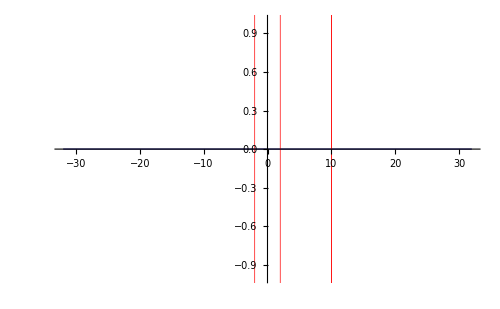

```mathematica
Redlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red}},None},ImageSize->500]
```

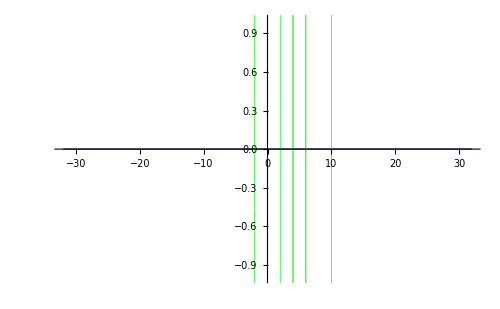

```mathematica
Greenlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

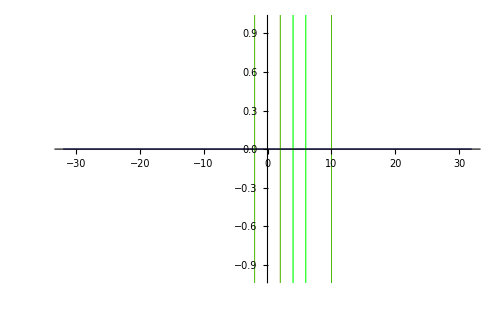

```mathematica
Alllines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red},{δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

```mathematica
Alllines1=Plot[0,{x,50,225},GridLines->{{ {eig1,Red},{eig2,Red},{eig3,Red},{eig4,Red},{eig5,Green},{eig6,Green},{eig7,Green},{eig8,Green},{eig9,Green},{eig10,Green},{eig11,Green},{eig12,Green}},None},ImageSize->500]
```

-Graphics-

## Deloc Case

```mathematica
g=0.5;
J=1;
ω0=100.005;
ωc=100;
```

### First manifold eigenstates

```mathematica
deloceig1= newevectab[[12]]//FullSimplify//N//Chop 
deloceig2=newevectab[[11]]//FullSimplify//N//Chop 
deloceig3=newevectab[[10]]//FullSimplify//N//Chop 
deloceig4=newevectab[[9]]//FullSimplify//N//Chop
```

0.27 |00eg>+0.27 |00ge>-0.65 |01gg>-0.65 |10gg>

0.65 |00eg>-0.65 |00ge>+0.27 |01gg>-0.27 |10gg>

0.65 |00eg>+0.65 |00ge>+0.27 |01gg>+0.27 |10gg>

0.27 |00eg>-0.27 |00ge>-0.65 |01gg>+0.65 |10gg>

### Second manifold eigenstates

```mathematica
deloceig5= newevectab[[8]]//FullSimplify//N//Chop 
deloceig6=newevectab[[7]]//FullSimplify//N//Chop 
deloceig7=newevectab[[6]]//FullSimplify//N//Chop 
deloceig8=newevectab[[5]]//FullSimplify//N//Chop 
deloceig9= newevectab[[4]]//FullSimplify//N//Chop 
deloceig10=newevectab[[3]]//FullSimplify//N//Chop 
deloceig11=newevectab[[2]]//FullSimplify//N//Chop 
deloceig12=newevectab[[1]]//FullSimplify//N//Chop
```

-0.1 |00ee>+0.25 |01eg>+0.23 |01ge>-0.43 |02gg>+0.23 |10eg>+0.25 |10ge>-0.62 |11gg>-0.43 |20gg>

-0.41 |01eg>+0.5 |01ge>-0.29 |02gg>-0.5 |10eg>+0.41 |10ge>+0.29 |20gg>

-0.49 |00ee>+0.43 |01eg>+0.29 |01ge>+0.25 |02gg>+0.29 |10eg>+0.43 |10ge>+0.3 |11gg>+0.25 |20gg>

0.41 |01eg>-0.58 |02gg>-0.41 |10ge>+0.58 |20gg>

-0.71 |00ee>-0.47 |01ge>-0.47 |10eg>-0.24 |11gg>

-0.49 |00ee>-0.43 |01eg>+0.29 |01ge>-0.25 |02gg>+0.29 |10eg>-0.43 |10ge>+0.3 |11gg>-0.25 |20gg>

0.41 |01eg>+0.5 |01ge>+0.29 |02gg>-0.5 |10eg>-0.41 |10ge>-0.29 |20gg>

0.1 |00ee>+0.25 |01eg>-0.23 |01ge>-0.43 |02gg>-0.23 |10eg>+0.25 |10ge>+0.62 |11gg>-0.43 |20gg>

```mathematica
deloceig10=newevectab[[3]]//FullSimplify//N//Chop 
deloceig8=newevectab[[5]]//FullSimplify//N//Chop 
deloceig5= newevectab[[8]]//FullSimplify//N//Chop
```

-0.49 |00ee>-0.43 |01eg>+0.29 |01ge>-0.25 |02gg>+0.29 |10eg>-0.43 |10ge>+0.3 |11gg>-0.25 |20gg>

0.41 |01eg>-0.58 |02gg>-0.41 |10ge>+0.58 |20gg>

-0.1 |00ee>+0.25 |01eg>+0.23 |01ge>-0.43 |02gg>+0.23 |10eg>+0.25 |10ge>-0.62 |11gg>-0.43 |20gg>

## Loc Case

```mathematica
g=5;
J=1;
ω0=100.005;
ωc=100;
```

### First manifold eigenstates

```mathematica
Loceig1= newevectab[[12]]//FullSimplify//N//Chop 
Loceig2=newevectab[[11]]//FullSimplify//N//Chop 
Loceig3=newevectab[[10]]//FullSimplify//N//Chop 
Loceig4=newevectab[[9]]//FullSimplify//N//Chop
```

0.47 |00eg>+0.47 |00ge>-0.52 |01gg>-0.52 |10gg>

0.52 |00eg>-0.52 |00ge>+0.47 |01gg>-0.47 |10gg>

0.52 |00eg>+0.52 |00ge>+0.47 |01gg>+0.47 |10gg>

0.47 |00eg>-0.47 |00ge>-0.52 |01gg>+0.52 |10gg>

### Second manifold eigenstates

```mathematica
Loceig5= newevectab[[8]]//FullSimplify//N//Chop 
Loceig6=newevectab[[7]]//FullSimplify//N//Chop 
Loceig7=newevectab[[6]]//FullSimplify//N//Chop 
Loceig8=newevectab[[5]]//FullSimplify//N//Chop 
Loceig9= newevectab[[4]]//FullSimplify//N//Chop 
Loceig10=newevectab[[3]]//FullSimplify//N//Chop 
Loceig11=newevectab[[2]]//FullSimplify//N//Chop 
Loceig12=newevectab[[1]]//FullSimplify//N//Chop
```

-0.45 |00ee>+0.47 |01eg>+0.17 |01ge>-0.18 |02gg>+0.17 |10eg>+0.47 |10ge>-0.5 |11gg>-0.18 |20gg>

-0.07 |01eg>+0.5 |01ge>-0.5 |02gg>-0.5 |10eg>+0.07 |10ge>+0.5 |20gg>

-0.27 |00ee>+0.18 |01eg>-0.46 |01ge>+0.47 |02gg>-0.46 |10eg>+0.18 |10ge>-0.07 |11gg>+0.47 |20gg>

0.68 |00ee>-0.14 |01ge>-0.14 |10eg>-0.71 |11gg>

-0.7 |01eg>+0.1 |02gg>+0.7 |10ge>-0.1 |20gg>

0.27 |00ee>+0.18 |01eg>+0.46 |01ge>+0.47 |02gg>+0.46 |10eg>+0.18 |10ge>+0.07 |11gg>+0.47 |20gg>

-0.07 |01eg>-0.5 |01ge>-0.49 |02gg>+0.5 |10eg>+0.07 |10ge>+0.49 |20gg>

-0.45 |00ee>-0.47 |01eg>+0.17 |01ge>+0.18 |02gg>+0.17 |10eg>-0.47 |10ge>-0.5 |11gg>+0.18 |20gg>

```mathematica
Loceig10=newevectab[[3]]//FullSimplify//N//Chop //FullSimplify
Loceig8=newevectab[[5]]//FullSimplify//N//Chop //FullSimplify
Loceig5= newevectab[[8]]//FullSimplify//N//Chop //FullSimplify
```

0.27 |00ee>+0.18 |01eg>+0.46 |01ge>+0.47 |02gg>+0.46 |10eg>+0.18 |10ge>+0.07 |11gg>+0.47 |20gg>

0.68 |00ee>-0.14 |01ge>-0.14 |10eg>-0.71 |11gg>

-0.45 |00ee>+0.47 |01eg>+0.17 |01ge>-0.18 |02gg>+0.17 |10eg>+0.47 |10ge>-0.5 |11gg>-0.18 |20gg>

## Atomic limit Case

```mathematica
g=0.5;
J=1;
ω0=100;
ωc=105;
```

### First manifold eigenstates

```mathematica
ALeig1= newevectab[[12]]//FullSimplify//N//Chop 
ALeig2=newevectab[[11]]//FullSimplify//N//Chop 
ALeig3=newevectab[[10]]//FullSimplify//N//Chop 
ALeig4=newevectab[[9]]//FullSimplify//N//Chop
```

-0.7 |00eg>-0.7 |00ge>+0.09 |01gg>+0.09 |10gg>

-0.7 |00eg>+0.7 |00ge>-0.06 |01gg>+0.06 |10gg>

-0.09 |00eg>-0.09 |00ge>-0.7 |01gg>-0.7 |10gg>

-0.06 |00eg>+0.06 |00ge>+0.7 |01gg>-0.7 |10gg>

### Second manifold eigenstates

```mathematica
ALeig5= newevectab[[8]]//FullSimplify//N//Chop 
ALeig6=newevectab[[7]]//FullSimplify//N//Chop 
ALeig7=newevectab[[6]]//FullSimplify//N//Chop 
ALeig8=newevectab[[5]]//FullSimplify//N//Chop 
ALeig9= newevectab[[4]]//FullSimplify//N//Chop 
ALeig10=newevectab[[3]]//FullSimplify//N//Chop 
ALeig11=newevectab[[2]]//FullSimplify//N//Chop 
ALeig12=newevectab[[1]]//FullSimplify//N//Chop
```

0.99 |00ee>-0.1 |01eg>-0.02 |01ge>-0.02 |10eg>-0.1 |10ge>+0.01 |11gg>

-0.12 |00ee>-0.47 |01eg>-0.5 |01ge>+0.09 |02gg>-0.5 |10eg>-0.47 |10ge>+0.12 |11gg>+0.09 |20gg>

-0.49 |01eg>+0.51 |01ge>-0.06 |02gg>-0.51 |10eg>+0.49 |10ge>+0.06 |20gg>

0.51 |01eg>+0.48 |01ge>-0.08 |02gg>-0.48 |10eg>-0.51 |10ge>+0.08 |20gg>

0.08 |00ee>+0.5 |01eg>-0.49 |01ge>+0.05 |02gg>-0.49 |10eg>+0.5 |10ge>-0.09 |11gg>+0.05 |20gg>

-0.01 |00ee>-0.09 |01eg>-0.08 |01ge>-0.49 |02gg>-0.08 |10eg>-0.09 |10ge>-0.7 |11gg>-0.49 |20gg>

-0.02 |01eg>-0.1 |01ge>-0.7 |02gg>+0.1 |10eg>+0.02 |10ge>+0.7 |20gg>

-0.06 |01eg>+0.06 |01ge>+0.5 |02gg>+0.06 |10eg>-0.06 |10ge>-0.7 |11gg>+0.5 |20gg>

```mathematica
ALeig10=newevectab[[3]]//FullSimplify//N//Chop //FullSimplify
ALeig8=newevectab[[5]]//FullSimplify//N//Chop //FullSimplify
ALeig5= newevectab[[8]]//FullSimplify//N//Chop //FullSimplify
```

-0.01 |00ee>-0.09 |01eg>-0.08 |01ge>-0.49 |02gg>-0.08 |10eg>-0.09 |10ge>-0.7 |11gg>-0.49 |20gg>

0.51 |01eg>+0.48 |01ge>-0.08 |02gg>-0.48 |10eg>-0.51 |10ge>+0.08 |20gg>

0.99 |00ee>-0.1 |01eg>-0.02 |01ge>-0.02 |10eg>-0.1 |10ge>+0.01 |11gg>

## Photonic limit Case

```mathematica
g=0.5;
J=1;
ω0=105;
ωc=100;
```

### First manifold eigenstates

```mathematica
ALeig1= newevectab[[12]]//FullSimplify//N//Chop 
ALeig2=newevectab[[11]]//FullSimplify//N//Chop 
ALeig3=newevectab[[10]]//FullSimplify//N//Chop 
ALeig4=newevectab[[9]]//FullSimplify//N//Chop
```

-0.06 |00eg>-0.06 |00ge>+0.7 |01gg>+0.7 |10gg>

0.09 |00eg>-0.09 |00ge>+0.7 |01gg>-0.7 |10gg>

0.7 |00eg>+0.7 |00ge>+0.06 |01gg>+0.06 |10gg>

-0.7 |00eg>+0.7 |00ge>+0.09 |01gg>-0.09 |10gg>

### Second manifold eigenstates

```mathematica
ALeig5= newevectab[[8]]//FullSimplify//N//Chop 
ALeig6=newevectab[[7]]//FullSimplify//N//Chop 
ALeig7=newevectab[[6]]//FullSimplify//N//Chop 
ALeig8=newevectab[[5]]//FullSimplify//N//Chop 
ALeig9= newevectab[[4]]//FullSimplify//N//Chop 
ALeig10=newevectab[[3]]//FullSimplify//N//Chop 
ALeig11=newevectab[[2]]//FullSimplify//N//Chop 
ALeig12=newevectab[[1]]//FullSimplify//N//Chop
```

0.06 |01eg>+0.06 |01ge>-0.5 |02gg>+0.06 |10eg>+0.06 |10ge>-0.7 |11gg>-0.5 |20gg>

-0.02 |01eg>+0.1 |01ge>-0.7 |02gg>-0.1 |10eg>+0.02 |10ge>+0.7 |20gg>

-0.01 |00ee>+0.09 |01eg>-0.08 |01ge>+0.49 |02gg>-0.08 |10eg>+0.09 |10ge>-0.7 |11gg>+0.49 |20gg>

0.08 |00ee>-0.5 |01eg>-0.49 |01ge>-0.05 |02gg>-0.49 |10eg>-0.5 |10ge>-0.09 |11gg>-0.05 |20gg>

0.51 |01eg>-0.48 |01ge>-0.08 |02gg>+0.48 |10eg>-0.51 |10ge>+0.08 |20gg>

-0.49 |01eg>-0.51 |01ge>-0.06 |02gg>+0.51 |10eg>+0.49 |10ge>+0.06 |20gg>

-0.12 |00ee>+0.47 |01eg>-0.5 |01ge>-0.09 |02gg>-0.5 |10eg>+0.47 |10ge>+0.12 |11gg>-0.09 |20gg>

0.99 |00ee>+0.1 |01eg>-0.02 |01ge>-0.02 |10eg>+0.1 |10ge>+0.01 |11gg>

```mathematica
ALeig10=newevectab[[3]]//FullSimplify//N//Chop //FullSimplify
ALeig8=newevectab[[5]]//FullSimplify//N//Chop //FullSimplify
ALeig5= newevectab[[8]]//FullSimplify//N//Chop //FullSimplify
```

-0.49 |01eg>-0.51 |01ge>-0.06 |02gg>+0.51 |10eg>+0.49 |10ge>+0.06 |20gg>

0.08 |00ee>-0.5 |01eg>-0.49 |01ge>-0.05 |02gg>-0.49 |10eg>-0.5 |10ge>-0.09 |11gg>-0.05 |20gg>

0.06 |01eg>+0.06 |01ge>-0.5 |02gg>+0.06 |10eg>+0.06 |10ge>-0.7 |11gg>-0.5 |20gg>

```mathematica
ωc=ω0;
```

```mathematica
{neweval,newevec}=Eigensystem[newHtot];
```

```mathematica
newevaltab={};
newevectab={};
Do[AppendTo[newevaltab,neweval[[i]]//Simplify],{i,1,13}]
Do[AppendTo[newevectab,(newevec[[i]]//Simplify).newbasisset],{i,1,13}]
```

```mathematica
newevaltab//MatrixForm
newevectab//MatrixForm
```

(0
2 ω0
2 ω0
-√(2 g^2+J^2)+2 ω0
√(2 g^2+J^2)+2 ω0
-J/2-1/2 √(4 g^2+J^2)+ω0
1/2 (J-√(4 g^2+J^2)+2 ω0)
1/2 (-J+√(4 g^2+J^2)+2 ω0)
1/2 (J+√(4 g^2+J^2)+2 ω0)
-(√(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)))/(√2)+2 ω0
(√(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)))/(√2)+2 ω0
-(√(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(√2)+2 ω0
(√(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(√2)+2 ω0)

(|00gg>
-|02gg>+|20gg>+(√2 |01eg> g)/J-(√2 |10ge> g)/J
|11gg>+(|01ge> J)/g+(|10eg> J)/g+|00ee> (-1+J^2/g^2)
-|02gg>+|20gg>-(|01eg> J)/(√2 g)+(|10ge> J)/(√2 g)+(|01ge> √(g^2+J^2/2))/g-(|10eg> √(g^2+J^2/2))/g
-|02gg>+|20gg>-(|01eg> J)/(√2 g)+(|10ge> J)/(√2 g)-(|01ge> √(g^2+J^2/2))/g+(|10eg> √(g^2+J^2/2))/g
|01gg>+|10gg>+(|00ge> (J-√(4 g^2+J^2)))/(2 g)-(2 |00eg> g)/(J+√(4 g^2+J^2))
-|01gg>+|10gg>+(2 |00eg> g)/(J-√(4 g^2+J^2))+(|00ge> (J+√(4 g^2+J^2)))/(2 g)
|01gg>+|10gg>+(2 |00eg> g)/(-J+√(4 g^2+J^2))+(|00ge> (J+√(4 g^2+J^2)))/(2 g)
-|01gg>+|10gg>+(|00ge> (J-√(4 g^2+J^2)))/(2 g)+(2 |00eg> g)/(J+√(4 g^2+J^2))
|02gg>+|20gg>+(|10ge> (-2 g^2+3 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(6 √2 g J)+(|00ee> g^2 √(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^2+15 J^2-√(4 g^4+60 g^2 J^2+9 J^4)))/(6 J (2 g^4+3 J^4-J^2 √(4 g^4+60 g^2 J^2+9 J^4)-g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|11gg> √(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^4+9 J^4-3 J^2 √(4 g^4+60 g^2 J^2+9 J^4)-g^2 (-21 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))/(6 J (2 g^4+3 J^4-J^2 √(4 g^4+60 g^2 J^2+9 J^4)-g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|01eg> g (-4 g^4-21 J^4+5 J^2 √(4 g^4+60 g^2 J^2+9 J^4)+2 g^2 (-20 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))/(3 √2 J (2 g^4+3 J^4-J^2 √(4 g^4+60 g^2 J^2+9 J^4)-g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|01ge> g √(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^2+6 J^2-√(4 g^4+60 g^2 J^2+9 J^4)))/(3 (-2 g^4+g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+J^2 (-3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|10eg> g √(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^2+6 J^2-√(4 g^4+60 g^2 J^2+9 J^4)))/(3 (-2 g^4+g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+J^2 (-3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))
|02gg>+|20gg>+(|10ge> (-2 g^2+3 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(6 √2 g J)+(|00ee> g^2 √(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)) (-2 g^2-15 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(6 J (2 g^4+3 J^4-J^2 √(4 g^4+60 g^2 J^2+9 J^4)-g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|01eg> g (-4 g^4-21 J^4+5 J^2 √(4 g^4+60 g^2 J^2+9 J^4)+2 g^2 (-20 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))/(3 √2 J (2 g^4+3 J^4-J^2 √(4 g^4+60 g^2 J^2+9 J^4)-g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|01ge> g √(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)) (-2 g^2-6 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(3 (-2 g^4+g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+J^2 (-3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|10eg> g √(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)) (-2 g^2-6 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(3 (-2 g^4+g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+J^2 (-3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|11gg> √(6 g^2+5 J^2-√(4 g^4+60 g^2 J^2+9 J^4)) (-2 g^4+g^2 (-21 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+3 J^2 (-3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))/(6 J (2 g^4+3 J^4-J^2 √(4 g^4+60 g^2 J^2+9 J^4)-g^2 (-11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))
|02gg>+|20gg>-(|10ge> (2 g^2-3 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(6 √2 g J)-(|01ge> g √(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^2+6 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(3 (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))-(|10eg> g √(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^2+6 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(3 (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|00ee> g^2 √(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^2+15 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(6 J (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))-(|01eg> g (4 g^4+21 J^4+5 J^2 √(4 g^4+60 g^2 J^2+9 J^4)+2 g^2 (20 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))/(3 √2 J (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|11gg> √(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^4+3 J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (21 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))/(6 J (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))
|02gg>+|20gg>-(|10ge> (2 g^2-3 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(6 √2 g J)+(|01ge> g √(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^2+6 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(3 (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))+(|10eg> g √(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^2+6 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(3 (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))-(|00ee> g^2 √(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^2+15 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))/(6 J (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))-(|01eg> g (4 g^4+21 J^4+5 J^2 √(4 g^4+60 g^2 J^2+9 J^4)+2 g^2 (20 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))/(3 √2 J (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))-(|11gg> √(6 g^2+5 J^2+√(4 g^4+60 g^2 J^2+9 J^4)) (2 g^4+3 J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (21 J^2+√(4 g^4+60 g^2 J^2+9 J^4))))/(6 J (2 g^4+J^2 (3 J^2+√(4 g^4+60 g^2 J^2+9 J^4))+g^2 (11 J^2+√(4 g^4+60 g^2 J^2+9 J^4)))))

### 2nd Simplification only g undefined wc w0

```mathematica
ω0=100;
ωc=100;
J=1;
```

```mathematica
{neweval,newevec}=Eigensystem[newHtot];
```

```mathematica
newevaltab={};
newevectab={};
Do[AppendTo[newevaltab,neweval[[i]]//Simplify],{i,1,13}]
Do[AppendTo[newevectab,(newevec[[i]]//Simplify).newbasisset],{i,1,13}]
```

```mathematica
newevaltab//MatrixForm
newevectab//MatrixForm
```

(200
200
0
200-√(1+2 g^2)
200+√(1+2 g^2)
1/2 (199-√(1+4 g^2))
1/2 (201-√(1+4 g^2))
1/2 (199+√(1+4 g^2))
1/2 (201+√(1+4 g^2))
200-(√(5+6 g^2-√(9+60 g^2+4 g^4)))/(√2)
200+(√(5+6 g^2-√(9+60 g^2+4 g^4)))/(√2)
200-(√(5+6 g^2+√(9+60 g^2+4 g^4)))/(√2)
200+(√(5+6 g^2+√(9+60 g^2+4 g^4)))/(√2))

(-|02gg>+|20gg>+√2 |01eg> g-√2 |10ge> g
|11gg>+|00ee> (-1+1/g^2)+(|01ge>)/g+(|10eg>)/g
|00gg>
-|02gg>+|20gg>-(|01eg>)/(√2 g)+(|10ge>)/(√2 g)-(|10eg> √(1/2+g^2))/g+(|01ge> (1+2 g^2) (100060001+g^4-4000400 √(1+2 g^2)+g^2 (100002-400 √(1+2 g^2))))/(√2 g (10001+g^2-200 √(1+2 g^2)) (-200+10001 √(1+2 g^2)+g^2 (-400+√(1+2 g^2))))
-|02gg>+|20gg>-(|01eg>)/(√2 g)+(|10ge>)/(√2 g)+(|10eg> √(1/2+g^2))/g-(|01ge> (1+2 g^2) (100060001+g^4+4000400 √(1+2 g^2)+2 g^2 (50001+200 √(1+2 g^2))))/(√2 g (10001+g^2+200 √(1+2 g^2)) (200+10001 √(1+2 g^2)+g^2 (400+√(1+2 g^2))))
|01gg>+|10gg>-(|00eg> (-1+√(1+4 g^2)))/(2 g)-(|00ge> (-1+√(1+4 g^2)))/(2 g)
-|01gg>+|10gg>-(|00eg> (1+√(1+4 g^2)))/(2 g)+(|00ge> (1+√(1+4 g^2)))/(2 g)
|01gg>+|10gg>+(|00eg> (1+√(1+4 g^2)))/(2 g)+(|00ge> (1+√(1+4 g^2)))/(2 g)
-|01gg>+|10gg>+(|00eg> (-1+√(1+4 g^2)))/(2 g)-(|00ge> (-1+√(1+4 g^2)))/(2 g)
|02gg>+|20gg>+(|10ge> g (-192 √2 g^14+1728 (-3+√(9+60 g^2+4 g^4)) (13899167 √2-69715325 √(5+6 g^2-√(9+60 g^2+4 g^4)))+16 g^12 (-453645 √2+6 √2 √(9+60 g^2+4 g^4)+1900 √(5+6 g^2-√(9+60 g^2+4 g^4)))+4 g^4 (-372063963893 √2+44739342505 √2 √(9+60 g^2+4 g^4)+833895363800 √(5+6 g^2-√(9+60 g^2+4 g^4))-65865997100 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-79509644022 √2+16537486934 √2 √(9+60 g^2+4 g^4)+307799456475 √(5+6 g^2-√(9+60 g^2+4 g^4))-53238868175 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-1051692316895 √2+65552793443 √2 √(9+60 g^2+4 g^4)+940243945300 √(5+6 g^2-√(9+60 g^2+4 g^4))-27919641300 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+2 g^8 (-105865718153 √2+2694058216 √2 √(9+60 g^2+4 g^4)+28680998400 √(5+6 g^2-√(9+60 g^2+4 g^4))-50784500 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+40 g^10 (-270766357 √2+90711 √2 √(9+60 g^2+4 g^4)+5084150 √(5+6 g^2-√(9+60 g^2+4 g^4))-380 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (100 √2-√(5+6 g^2-√(9+60 g^2+4 g^4))) (-3-2 g^4+√(9+60 g^2+4 g^4)+g^2 (-12+√(9+60 g^2+4 g^4))) (12 (-3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (-3200 √2+6 √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2-√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))-(|10eg> g (48 g^8-2 g^6 (-586999+12 √(9+60 g^2+4 g^4)+1600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+5 g^4 (108995009-117365 √(9+60 g^2+4 g^4)-2140080 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+320 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+4 g^2 (886920263-67171715 √(9+60 g^2+4 g^4)-17677600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1334850 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+4 (325702536-91892512 √(9+60 g^2+4 g^4)-6502125 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1834025 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (12 (-3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (-3200 √2+6 √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2-√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))+(2 |11gg> (12 g^10+g^8 (293564-6 √(9+60 g^2+4 g^4)-800 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+72 (-3+√(9+60 g^2+4 g^4)) (-2784167+55575 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (137934445-146737 √(9+60 g^2+4 g^4)-2679600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+2 g^4 (873710773-33933427 √(9+60 g^2+4 g^4)-17354300 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+668400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+4 g^2 (727402662-92092534 √(9+60 g^2+4 g^4)-14507325 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1834625 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (12 (-3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (-3200 √2+6 √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2-√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))-(4 |01ge> g (1536 g^16-256 g^14 (-321839+3 √(9+60 g^2+4 g^4)+550 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+13824 (-3+√(9+60 g^2+4 g^4)) (-6985431667+208597250 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+32 g^12 (7798893287-1287176 √(9+60 g^2+4 g^4)-48113600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+2200 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+4 g^10 (12067119955397-31118347772 √(9+60 g^2+4 g^4)-328732727000 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+192322400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (889504585116088-23201801442478 √(9+60 g^2+4 g^4)-25828199055000 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+651697682800 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+20 g^2 (130484894357868-27433910228188 √(9+60 g^2+4 g^4)-3892519548795 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+817898718935 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+4 g^4 (1558038787764169-188087701587733 √(9+60 g^2+4 g^4)-46366987746050 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+5585522222400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (4412593368369023-274091279333651 √(9+60 g^2+4 g^4)-130505857869900 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+8047123544700 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (-5-2 g^2+√(9+60 g^2+4 g^4)) (-100 √2+√(5+6 g^2-√(9+60 g^2+4 g^4)))^2 (-3-2 g^4+√(9+60 g^2+4 g^4)+g^2 (-12+√(9+60 g^2+4 g^4))) (12 (-3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (-3200 √2+6 √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2-√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))-(16 |00ee> g^2 (768 g^18-64 g^16 (-643765+6 √(9+60 g^2+4 g^4)+1100 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+27648 (-3+√(9+60 g^2+4 g^4)) (-6985431667+208597250 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+32 g^14 (3908779637-643675 √(9+60 g^2+4 g^4)-24072750 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1100 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+16 g^12 (1564895768879-3899125160 √(9+60 g^2+4 g^4)-41440352600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+24056250 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^10 (77246887576871-1506478398659 √(9+60 g^2+4 g^4)-2208738235300 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+41079627650 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+20 g^2 (285161510561388-62898347735260 √(9+60 g^2+4 g^4)-8507451593595 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1875601336535 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+2 g^8 (2552267710159045-110139549083116 √(9+60 g^2+4 g^4)-74857945575600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+3190280227100 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+4 g^4 (4023157564566289-547141678526717 √(9+60 g^2+4 g^4)-119787417694100 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+16265483757050 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (15323572732710391-1212979425413419 √(9+60 g^2+4 g^4)-454209238137100 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+35799065781900 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (-5-2 g^2+√(9+60 g^2+4 g^4))^2 (-100 √2+√(5+6 g^2-√(9+60 g^2+4 g^4)))^2 (-3-2 g^4+√(9+60 g^2+4 g^4)+g^2 (-12+√(9+60 g^2+4 g^4))) (12 (-3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (-3200 √2+6 √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2-√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))+(4 |01eg> g (256 g^18 (-4400+3 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))-27648 (-3+√(9+60 g^2+4 g^4)) (-3337556000+6985431667 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-19043800031991600+2047152354431600 √(9+60 g^2+4 g^4)+15323572732710391 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))-1212979425413419 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (-11878903231386400+792826176227200 √(9+60 g^2+4 g^4)+5104535420318090 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))-220279098166232 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-64 g^16 (192626000-8800 √(9+60 g^2+4 g^4)-643765 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+6 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-32 g^14 (332485493200-192494000 √(9+60 g^2+4 g^4)-3908779637 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+643675 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-16 g^12 (19322323836400-329599033600 √(9+60 g^2+4 g^4)-1564895768879 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+3899125160 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-8 g^10 (378908124972400-14399113428400 √(9+60 g^2+4 g^4)-77246887576871 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1506478398659 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-80 g^2 (40955063695995-9807823653335 √(9+60 g^2+4 g^4)-71290377640347 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+15724586933815 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-4 g^4 (3137995375640600-514765753150800 √(9+60 g^2+4 g^4)-4023157564566289 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+547141678526717 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (-5-2 g^2+√(9+60 g^2+4 g^4))^2 (-100 √2+√(5+6 g^2-√(9+60 g^2+4 g^4)))^2 (-3-2 g^4+√(9+60 g^2+4 g^4)+g^2 (-12+√(9+60 g^2+4 g^4))) (12 (-3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (-3200 √2+6 √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2-√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))
|02gg>+|20gg>-(|10ge> g (192 √2 g^14+g^12 (7258320 √2-96 √2 √(9+60 g^2+4 g^4)+30400 √(5+6 g^2-√(9+60 g^2+4 g^4)))-1728 (-3+√(9+60 g^2+4 g^4)) (13899167 √2+69715325 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (1051692316895 √2-65552793443 √2 √(9+60 g^2+4 g^4)+940243945300 √(5+6 g^2-√(9+60 g^2+4 g^4))-27919641300 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (211731436306 √2-5388116432 √2 √(9+60 g^2+4 g^4)+57361996800 √(5+6 g^2-√(9+60 g^2+4 g^4))-101569000 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-40 g^10 (-270766357 √2+90711 √2 √(9+60 g^2+4 g^4)-5084150 √(5+6 g^2-√(9+60 g^2+4 g^4))+380 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-8 g^2 (-79509644022 √2+16537486934 √2 √(9+60 g^2+4 g^4)-307799456475 √(5+6 g^2-√(9+60 g^2+4 g^4))+53238868175 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-4 g^4 (-372063963893 √2+44739342505 √2 √(9+60 g^2+4 g^4)-833895363800 √(5+6 g^2-√(9+60 g^2+4 g^4))+65865997100 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (100 √2+√(5+6 g^2-√(9+60 g^2+4 g^4))) (-3-2 g^4+√(9+60 g^2+4 g^4)+g^2 (-12+√(9+60 g^2+4 g^4))) (-2 g^8 (1600 √2+3 √(5+6 g^2-√(9+60 g^2+4 g^4)))+12 (-3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2-√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))-(|10eg> g (48 g^8+g^6 (1173998-24 √(9+60 g^2+4 g^4)+3200 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+4 (325702536-91892512 √(9+60 g^2+4 g^4)+6502125 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))-1834025 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-5 g^4 (-108995009+117365 √(9+60 g^2+4 g^4)-2140080 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+320 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-4 g^2 (-886920263+67171715 √(9+60 g^2+4 g^4)-17677600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1334850 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (-2 g^8 (1600 √2+3 √(5+6 g^2-√(9+60 g^2+4 g^4)))+12 (-3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2-√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))-(2 |11gg> (-12 g^10+g^8 (-293564+6 √(9+60 g^2+4 g^4)-800 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+72 (-3+√(9+60 g^2+4 g^4)) (2784167+55575 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-137934445+146737 √(9+60 g^2+4 g^4)-2679600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+2 g^4 (-873710773+33933427 √(9+60 g^2+4 g^4)-17354300 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+668400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+4 g^2 (-727402662+92092534 √(9+60 g^2+4 g^4)-14507325 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1834625 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (-2 g^8 (1600 √2+3 √(5+6 g^2-√(9+60 g^2+4 g^4)))+12 (-3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2-√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))-(4 |01ge> g (1536 g^16-256 g^14 (-321839+3 √(9+60 g^2+4 g^4)-550 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))-13824 (-3+√(9+60 g^2+4 g^4)) (6985431667+208597250 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (4412593368369023-274091279333651 √(9+60 g^2+4 g^4)+130505857869900 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))-8047123544700 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (889504585116088-23201801442478 √(9+60 g^2+4 g^4)+25828199055000 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))-651697682800 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-32 g^12 (-7798893287+1287176 √(9+60 g^2+4 g^4)-48113600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+2200 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-4 g^10 (-12067119955397+31118347772 √(9+60 g^2+4 g^4)-328732727000 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+192322400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-20 g^2 (-130484894357868+27433910228188 √(9+60 g^2+4 g^4)-3892519548795 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+817898718935 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-4 g^4 (-1558038787764169+188087701587733 √(9+60 g^2+4 g^4)-46366987746050 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+5585522222400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (-5-2 g^2+√(9+60 g^2+4 g^4)) (100 √2+√(5+6 g^2-√(9+60 g^2+4 g^4)))^2 (-3-2 g^4+√(9+60 g^2+4 g^4)+g^2 (-12+√(9+60 g^2+4 g^4))) (-2 g^8 (1600 √2+3 √(5+6 g^2-√(9+60 g^2+4 g^4)))+12 (-3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2-√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))-(16 |00ee> g^2 (768 g^18-64 g^16 (-643765+6 √(9+60 g^2+4 g^4)-1100 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))-27648 (-3+√(9+60 g^2+4 g^4)) (6985431667+208597250 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (15323572732710391-1212979425413419 √(9+60 g^2+4 g^4)+454209238137100 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))-35799065781900 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (5104535420318090-220279098166232 √(9+60 g^2+4 g^4)+149715891151200 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))-6380560454200 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-32 g^14 (-3908779637+643675 √(9+60 g^2+4 g^4)-24072750 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1100 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-16 g^12 (-1564895768879+3899125160 √(9+60 g^2+4 g^4)-41440352600 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+24056250 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-8 g^10 (-77246887576871+1506478398659 √(9+60 g^2+4 g^4)-2208738235300 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+41079627650 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-20 g^2 (-285161510561388+62898347735260 √(9+60 g^2+4 g^4)-8507451593595 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1875601336535 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-4 g^4 (-4023157564566289+547141678526717 √(9+60 g^2+4 g^4)-119787417694100 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+16265483757050 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (-5-2 g^2+√(9+60 g^2+4 g^4))^2 (100 √2+√(5+6 g^2-√(9+60 g^2+4 g^4)))^2 (-3-2 g^4+√(9+60 g^2+4 g^4)+g^2 (-12+√(9+60 g^2+4 g^4))) (-2 g^8 (1600 √2+3 √(5+6 g^2-√(9+60 g^2+4 g^4)))+12 (-3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2-√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))-(4 |01eg> g (256 g^18 (4400+3 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))-27648 (-3+√(9+60 g^2+4 g^4)) (3337556000+6985431667 √2 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (19043800031991600-2047152354431600 √(9+60 g^2+4 g^4)+15323572732710391 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))-1212979425413419 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^8 (11878903231386400-792826176227200 √(9+60 g^2+4 g^4)+5104535420318090 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))-220279098166232 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-64 g^16 (-192626000+8800 √(9+60 g^2+4 g^4)-643765 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+6 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-32 g^14 (-332485493200+192494000 √(9+60 g^2+4 g^4)-3908779637 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+643675 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-16 g^12 (-19322323836400+329599033600 √(9+60 g^2+4 g^4)-1564895768879 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+3899125160 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-8 g^10 (-378908124972400+14399113428400 √(9+60 g^2+4 g^4)-77246887576871 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+1506478398659 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-80 g^2 (-40955063695995+9807823653335 √(9+60 g^2+4 g^4)-71290377640347 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+15724586933815 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))-4 g^4 (-3137995375640600+514765753150800 √(9+60 g^2+4 g^4)-4023157564566289 √2 √(5+6 g^2-√(9+60 g^2+4 g^4))+547141678526717 √2 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))/(3 (-5-2 g^2+√(9+60 g^2+4 g^4))^2 (100 √2+√(5+6 g^2-√(9+60 g^2+4 g^4)))^2 (-3-2 g^4+√(9+60 g^2+4 g^4)+g^2 (-12+√(9+60 g^2+4 g^4))) (-2 g^8 (1600 √2+3 √(5+6 g^2-√(9+60 g^2+4 g^4)))+12 (-3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^6 (-10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2-√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+g^4 (-93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2-√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))+8 g^2 (-11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2-√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2-√(9+60 g^2+4 g^4)))))
|02gg>+|20gg>-(|10ge> g (192 √2 g^14+1728 (3+√(9+60 g^2+4 g^4)) (13899167 √2-69715325 √(5+6 g^2+√(9+60 g^2+4 g^4)))+16 g^12 (453645 √2+6 √2 √(9+60 g^2+4 g^4)-1900 √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 g^4 (372063963893 √2+44739342505 √2 √(9+60 g^2+4 g^4)-833895363800 √(5+6 g^2+√(9+60 g^2+4 g^4))-65865997100 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (79509644022 √2+16537486934 √2 √(9+60 g^2+4 g^4)-307799456475 √(5+6 g^2+√(9+60 g^2+4 g^4))-53238868175 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (1051692316895 √2+65552793443 √2 √(9+60 g^2+4 g^4)-940243945300 √(5+6 g^2+√(9+60 g^2+4 g^4))-27919641300 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+2 g^8 (105865718153 √2+2694058216 √2 √(9+60 g^2+4 g^4)-28680998400 √(5+6 g^2+√(9+60 g^2+4 g^4))-50784500 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+40 g^10 (270766357 √2+90711 √2 √(9+60 g^2+4 g^4)-5084150 √(5+6 g^2+√(9+60 g^2+4 g^4))-380 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (3+2 g^4+√(9+60 g^2+4 g^4)+g^2 (12+√(9+60 g^2+4 g^4))) (100 √2-√(5+6 g^2+√(9+60 g^2+4 g^4))) (12 (3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^8 (3200 √2-6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2+√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))+(|10eg> g (48 g^8+2 g^6 (586999+12 √(9+60 g^2+4 g^4)-1600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 (325702536+91892512 √(9+60 g^2+4 g^4)-6502125 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))-1834025 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-5 g^4 (-108995009-117365 √(9+60 g^2+4 g^4)+2140080 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+320 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-4 g^2 (-886920263-67171715 √(9+60 g^2+4 g^4)+17677600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1334850 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (12 (3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^8 (3200 √2-6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2+√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))-(2 |11gg> (12 g^10+g^8 (293564+6 √(9+60 g^2+4 g^4)-800 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))-72 (3+√(9+60 g^2+4 g^4)) (-2784167+55575 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (137934445+146737 √(9+60 g^2+4 g^4)-2679600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))-400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-2 g^4 (-873710773-33933427 √(9+60 g^2+4 g^4)+17354300 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+668400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-4 g^2 (-727402662-92092534 √(9+60 g^2+4 g^4)+14507325 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1834625 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (12 (3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^8 (3200 √2-6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2+√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))+(4 |01ge> g (1536 g^16+256 g^14 (321839+3 √(9+60 g^2+4 g^4)-550 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))-13824 (3+√(9+60 g^2+4 g^4)) (-6985431667+208597250 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (4412593368369023+274091279333651 √(9+60 g^2+4 g^4)-130505857869900 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))-8047123544700 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^8 (889504585116088+23201801442478 √(9+60 g^2+4 g^4)-25828199055000 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))-651697682800 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-32 g^12 (-7798893287-1287176 √(9+60 g^2+4 g^4)+48113600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+2200 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-4 g^10 (-12067119955397-31118347772 √(9+60 g^2+4 g^4)+328732727000 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+192322400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-20 g^2 (-130484894357868-27433910228188 √(9+60 g^2+4 g^4)+3892519548795 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+817898718935 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-4 g^4 (-1558038787764169-188087701587733 √(9+60 g^2+4 g^4)+46366987746050 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+5585522222400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (5+2 g^2+√(9+60 g^2+4 g^4)) (3+2 g^4+√(9+60 g^2+4 g^4)+g^2 (12+√(9+60 g^2+4 g^4))) (-100 √2+√(5+6 g^2+√(9+60 g^2+4 g^4)))^2 (12 (3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^8 (3200 √2-6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2+√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))-(16 |00ee> g^2 (768 g^18+64 g^16 (643765+6 √(9+60 g^2+4 g^4)-1100 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))-27648 (3+√(9+60 g^2+4 g^4)) (-6985431667+208597250 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (15323572732710391+1212979425413419 √(9+60 g^2+4 g^4)-454209238137100 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))-35799065781900 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^8 (5104535420318090+220279098166232 √(9+60 g^2+4 g^4)-149715891151200 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))-6380560454200 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-32 g^14 (-3908779637-643675 √(9+60 g^2+4 g^4)+24072750 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1100 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-16 g^12 (-1564895768879-3899125160 √(9+60 g^2+4 g^4)+41440352600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+24056250 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-8 g^10 (-77246887576871-1506478398659 √(9+60 g^2+4 g^4)+2208738235300 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+41079627650 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-20 g^2 (-285161510561388-62898347735260 √(9+60 g^2+4 g^4)+8507451593595 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1875601336535 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))-4 g^4 (-4023157564566289-547141678526717 √(9+60 g^2+4 g^4)+119787417694100 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+16265483757050 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (5+2 g^2+√(9+60 g^2+4 g^4))^2 (3+2 g^4+√(9+60 g^2+4 g^4)+g^2 (12+√(9+60 g^2+4 g^4))) (-100 √2+√(5+6 g^2+√(9+60 g^2+4 g^4)))^2 (12 (3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^8 (3200 √2-6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2+√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))+(4 |01eg> g (256 g^18 (-4400+3 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+27648 (3+√(9+60 g^2+4 g^4)) (-3337556000+6985431667 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+64 g^16 (-192626000-8800 √(9+60 g^2+4 g^4)+643765 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+6 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+32 g^14 (-332485493200-192494000 √(9+60 g^2+4 g^4)+3908779637 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+643675 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+16 g^12 (-19322323836400-329599033600 √(9+60 g^2+4 g^4)+1564895768879 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+3899125160 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^10 (-378908124972400-14399113428400 √(9+60 g^2+4 g^4)+77246887576871 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1506478398659 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+80 g^2 (-40955063695995-9807823653335 √(9+60 g^2+4 g^4)+71290377640347 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+15724586933815 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+2 g^8 (-5939451615693200-396413088113600 √(9+60 g^2+4 g^4)+2552267710159045 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+110139549083116 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 g^4 (-3137995375640600-514765753150800 √(9+60 g^2+4 g^4)+4023157564566289 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+547141678526717 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (-19043800031991600-2047152354431600 √(9+60 g^2+4 g^4)+15323572732710391 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1212979425413419 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (5+2 g^2+√(9+60 g^2+4 g^4))^2 (3+2 g^4+√(9+60 g^2+4 g^4)+g^2 (12+√(9+60 g^2+4 g^4))) (-100 √2+√(5+6 g^2+√(9+60 g^2+4 g^4)))^2 (12 (3+√(9+60 g^2+4 g^4)) (444600 √2-2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^8 (3200 √2-6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)-46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))-4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)-67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))-73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)-146745 √(5+6 g^2+√(9+60 g^2+4 g^4))-3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))
|02gg>+|20gg>-(|10ge> g (192 √2 g^14+16 g^12 (453645 √2+6 √2 √(9+60 g^2+4 g^4)+1900 √(5+6 g^2+√(9+60 g^2+4 g^4)))+1728 (3+√(9+60 g^2+4 g^4)) (13899167 √2+69715325 √(5+6 g^2+√(9+60 g^2+4 g^4)))+40 g^10 (270766357 √2+90711 √2 √(9+60 g^2+4 g^4)+5084150 √(5+6 g^2+√(9+60 g^2+4 g^4))+380 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+2 g^8 (105865718153 √2+2694058216 √2 √(9+60 g^2+4 g^4)+28680998400 √(5+6 g^2+√(9+60 g^2+4 g^4))+50784500 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (1051692316895 √2+65552793443 √2 √(9+60 g^2+4 g^4)+940243945300 √(5+6 g^2+√(9+60 g^2+4 g^4))+27919641300 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (79509644022 √2+16537486934 √2 √(9+60 g^2+4 g^4)+307799456475 √(5+6 g^2+√(9+60 g^2+4 g^4))+53238868175 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 g^4 (372063963893 √2+44739342505 √2 √(9+60 g^2+4 g^4)+833895363800 √(5+6 g^2+√(9+60 g^2+4 g^4))+65865997100 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (3+2 g^4+√(9+60 g^2+4 g^4)+g^2 (12+√(9+60 g^2+4 g^4))) (100 √2+√(5+6 g^2+√(9+60 g^2+4 g^4))) (g^8 (3200 √2+6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+12 (3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2+√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))+(|10eg> g (48 g^8+2 g^6 (586999+12 √(9+60 g^2+4 g^4)+1600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+5 g^4 (108995009+117365 √(9+60 g^2+4 g^4)+2140080 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+320 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 g^2 (886920263+67171715 √(9+60 g^2+4 g^4)+17677600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1334850 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 (325702536+91892512 √(9+60 g^2+4 g^4)+6502125 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1834025 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (g^8 (3200 √2+6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+12 (3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2+√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))-(2 |11gg> (12 g^10+g^8 (293564+6 √(9+60 g^2+4 g^4)+800 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+72 (3+√(9+60 g^2+4 g^4)) (2784167+55575 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (137934445+146737 √(9+60 g^2+4 g^4)+2679600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+2 g^4 (873710773+33933427 √(9+60 g^2+4 g^4)+17354300 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+668400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 g^2 (727402662+92092534 √(9+60 g^2+4 g^4)+14507325 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1834625 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (g^8 (3200 √2+6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+12 (3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2+√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))+(4 |01ge> g (1536 g^16+256 g^14 (321839+3 √(9+60 g^2+4 g^4)+550 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+13824 (3+√(9+60 g^2+4 g^4)) (6985431667+208597250 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+32 g^12 (7798893287+1287176 √(9+60 g^2+4 g^4)+48113600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+2200 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 g^10 (12067119955397+31118347772 √(9+60 g^2+4 g^4)+328732727000 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+192322400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^8 (889504585116088+23201801442478 √(9+60 g^2+4 g^4)+25828199055000 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+651697682800 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+20 g^2 (130484894357868+27433910228188 √(9+60 g^2+4 g^4)+3892519548795 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+817898718935 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 g^4 (1558038787764169+188087701587733 √(9+60 g^2+4 g^4)+46366987746050 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+5585522222400 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (4412593368369023+274091279333651 √(9+60 g^2+4 g^4)+130505857869900 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+8047123544700 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (5+2 g^2+√(9+60 g^2+4 g^4)) (3+2 g^4+√(9+60 g^2+4 g^4)+g^2 (12+√(9+60 g^2+4 g^4))) (100 √2+√(5+6 g^2+√(9+60 g^2+4 g^4)))^2 (g^8 (3200 √2+6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+12 (3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2+√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))-(16 |00ee> g^2 (768 g^18+64 g^16 (643765+6 √(9+60 g^2+4 g^4)+1100 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+27648 (3+√(9+60 g^2+4 g^4)) (6985431667+208597250 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+32 g^14 (3908779637+643675 √(9+60 g^2+4 g^4)+24072750 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1100 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+16 g^12 (1564895768879+3899125160 √(9+60 g^2+4 g^4)+41440352600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+24056250 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^10 (77246887576871+1506478398659 √(9+60 g^2+4 g^4)+2208738235300 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+41079627650 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+20 g^2 (285161510561388+62898347735260 √(9+60 g^2+4 g^4)+8507451593595 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1875601336535 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+2 g^8 (2552267710159045+110139549083116 √(9+60 g^2+4 g^4)+74857945575600 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+3190280227100 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 g^4 (4023157564566289+547141678526717 √(9+60 g^2+4 g^4)+119787417694100 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+16265483757050 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (15323572732710391+1212979425413419 √(9+60 g^2+4 g^4)+454209238137100 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+35799065781900 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (5+2 g^2+√(9+60 g^2+4 g^4))^2 (3+2 g^4+√(9+60 g^2+4 g^4)+g^2 (12+√(9+60 g^2+4 g^4))) (100 √2+√(5+6 g^2+√(9+60 g^2+4 g^4)))^2 (g^8 (3200 √2+6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+12 (3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2+√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))-(4 |01eg> g (256 g^18 (4400+3 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+27648 (3+√(9+60 g^2+4 g^4)) (3337556000+6985431667 √2 √(5+6 g^2+√(9+60 g^2+4 g^4)))+64 g^16 (192626000+8800 √(9+60 g^2+4 g^4)+643765 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+6 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+32 g^14 (332485493200+192494000 √(9+60 g^2+4 g^4)+3908779637 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+643675 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+16 g^12 (19322323836400+329599033600 √(9+60 g^2+4 g^4)+1564895768879 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+3899125160 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^10 (378908124972400+14399113428400 √(9+60 g^2+4 g^4)+77246887576871 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1506478398659 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+80 g^2 (40955063695995+9807823653335 √(9+60 g^2+4 g^4)+71290377640347 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+15724586933815 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+2 g^8 (5939451615693200+396413088113600 √(9+60 g^2+4 g^4)+2552267710159045 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+110139549083116 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+4 g^4 (3137995375640600+514765753150800 √(9+60 g^2+4 g^4)+4023157564566289 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+547141678526717 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (19043800031991600+2047152354431600 √(9+60 g^2+4 g^4)+15323572732710391 √2 √(5+6 g^2+√(9+60 g^2+4 g^4))+1212979425413419 √2 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))))/(3 (5+2 g^2+√(9+60 g^2+4 g^4))^2 (3+2 g^4+√(9+60 g^2+4 g^4)+g^2 (12+√(9+60 g^2+4 g^4))) (100 √2+√(5+6 g^2+√(9+60 g^2+4 g^4)))^2 (g^8 (3200 √2+6 √(5+6 g^2+√(9+60 g^2+4 g^4)))+12 (3+√(9+60 g^2+4 g^4)) (444600 √2+2784167 √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^6 (10706400 √2+1600 √2 √(9+60 g^2+4 g^4)+146745 √(5+6 g^2+√(9+60 g^2+4 g^4))+3 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+g^4 (93418400 √2+5342000 √2 √(9+60 g^2+4 g^4)+67986845 √(5+6 g^2+√(9+60 g^2+4 g^4))+73351 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4)))+8 g^2 (11838925 √2+1834425 √2 √(9+60 g^2+4 g^4)+46003762 √(5+6 g^2+√(9+60 g^2+4 g^4))+4192919 √(9+60 g^2+4 g^4) √(5+6 g^2+√(9+60 g^2+4 g^4))))))

### 3 rd simplification g -> 0

```mathematica
newevaltab1=Limit[newevaltab,g->10.^-10]//MatrixForm//Chop
newevectab1=Limit[newevectab,g->10.^-10]//MatrixForm//Chop
```

(200
200
0
199.
201.
99.
100.
100.
101.
199.
201.
198.
202.)

(1.41421×10^-10 |01eg>-1. |02gg>-1.41421×10^-10 |10ge>+|20gg>
1.×10^20 |00ee>+1.×10^10 |01ge>+1.×10^10 |10eg>+1. |11gg>
|00gg>
-7.07107×10^9 |01eg>+7.07107×10^9 |01ge>-1. |02gg>-7.07107×10^9 |10eg>+7.07107×10^9 |10ge>+|20gg>
-7.07107×10^9 |01eg>-7.07107×10^9 |01ge>-1. |02gg>+7.07107×10^9 |10eg>+7.07107×10^9 |10ge>+|20gg>
1. |01gg>+1. |10gg>
-1.×10^10 |00eg>+1.×10^10 |00ge>-1. |01gg>+1. |10gg>
1.×10^10 |00eg>+1.×10^10 |00ge>+1. |01gg>+1. |10gg>
-1. |01gg>+1. |10gg>
-1.41421 |00ee>+7.07107×10^9 |01eg>+7.07107×10^9 |01ge>+|02gg>+7.07107×10^9 |10eg>+7.07107×10^9 |10ge>+1.41421 |11gg>+|20gg>
1.41421 |00ee>+7.07107×10^9 |01eg>-7.07107×10^9 |01ge>+|02gg>-7.07107×10^9 |10eg>+7.07107×10^9 |10ge>-1.41421 |11gg>+|20gg>
-1.41421×10^-10 |01eg>-1.41421×10^-10 |01ge>+|02gg>-1.41421×10^-10 |10eg>-1.41421×10^-10 |10ge>+1.41421 |11gg>+|20gg>
-1.41421×10^-10 |01eg>+1.41421×10^-10 |01ge>+|02gg>+1.41421×10^-10 |10eg>-1.41421×10^-10 |10ge>-1.41421 |11gg>+|20gg>)

### 4 d simplification g = 10.^-8

```mathematica
J=1;
ωc=100;
ω0=100;
g=10.^-6;
```

```mathematica
newevaltab//MatrixForm//Simplify
newevectab//MatrixForm//Simplify//Chop
```

(200
200
0
199.
201.
99.
100.
100.
101.
199.
201.
198.
202.)

(1.41421×10^-6 |01eg>-|02gg>-1.41421×10^-6 |10ge>+|20gg>
1.×10^12 |00ee>+1.×10^6 |01ge>+1.×10^6 |10eg>+|11gg>
|00gg>
-707107. |01eg>+707107. |01ge>-|02gg>-707107. |10eg>+707107. |10ge>+|20gg>
-707107. |01eg>-707107. |01ge>-|02gg>+707107. |10eg>+707107. |10ge>+|20gg>
-9.99978×10^-7 |00eg>-9.99978×10^-7 |00ge>+|01gg>+|10gg>
-1.×10^6 |00eg>+1.×10^6 |00ge>-|01gg>+|10gg>
1.×10^6 |00eg>+1.×10^6 |00ge>+|01gg>+|10gg>
9.99978×10^-7 |00eg>-9.99978×10^-7 |00ge>-|01gg>+|10gg>
-1.4142 |00ee>+707089. |01eg>+707072. |01ge>+|02gg>+707107. |10eg>+707047. |10ge>+1.41421 |11gg>+|20gg>
1.4142 |00ee>+707110. |01eg>-707072. |01ge>+|02gg>-707106. |10eg>+707048. |10ge>-1.41421 |11gg>+|20gg>
-1.41421×10^-6 |01eg>-1.41421×10^-6 |01ge>+|02gg>-1.41421×10^-6 |10eg>-1.41421×10^-6 |10ge>+1.41421 |11gg>+|20gg>
-1.41421×10^-6 |01eg>+1.41421×10^-6 |01ge>+|02gg>+1.41421×10^-6 |10eg>-1.41421×10^-6 |10ge>-1.41421 |11gg>+|20gg>)

### 5 d simplification g >> 1

```mathematica
ω0=ωc;
ωc=0;
J=1;
```

```mathematica
newevaltab1=Limit[newevaltab,g->10.^6]//MatrixForm//Chop
newevectab1=Limit[newevectab,g->10.^6]//MatrixForm//Chop
```

(0
-1.×10^6
1.×10^6
-1.×10^6
1.×10^6
-1.41421×10^6
1.41421×10^6
0
-2.×10^6
-1.41421×10^6
1.41421×10^6
2.×10^6
0)

(|00gg>
-1. |00eg>-1. |00ge>+|01gg>+|10gg>
1. |00eg>+1. |00ge>+|01gg>+|10gg>
-1. |00eg>+1. |00ge>-1. |01gg>+|10gg>
1. |00eg>-1. |00ge>-1. |01gg>+|10gg>
-7.07107×10^-7 |01eg>+1. |01ge>-1. |02gg>-1. |10eg>+7.07107×10^-7 |10ge>+1. |20gg>
-7.07107×10^-7 |01eg>-1. |01ge>-1. |02gg>+1. |10eg>+7.07107×10^-7 |10ge>+1. |20gg>
ComplexInfinity
471405. |00ee>-471405. |01eg>-0.942809 |01ge>+|02gg>-0.942809 |10eg>-471405. |10ge>+471405. |11gg>+|20gg>
-3.0003×10^-6 |00ee>+2.12132×10^-6 |01eg>-1. |01ge>+|02gg>-1. |10eg>+2.12132×10^-6 |10ge>-1.×10^-6 |11gg>+|20gg>
2.99995×10^-6 |00ee>+2.12161×10^-6 |01eg>+1. |01ge>+|02gg>+1. |10eg>+2.12161×10^-6 |10ge>+1.00041×10^-6 |11gg>+|20gg>
-471405. |00ee>-471405. |01eg>+0.942809 |01ge>+|02gg>+0.942809 |10eg>-471405. |10ge>-471405. |11gg>+|20gg>
ComplexInfinity)

```mathematica
ToRadicals[Root[2 g^2 ω0+2 g^2 ωc+2 J^2 ωc-2 ω0^2 ωc-4 ω0 ωc^2-2 ωc^3+(-2 g^2-J^2+ω0^2+6 ω0 ωc+5 ωc^2) #1+(-2 ω0-4 ωc) #1^2+#1^3&,1]]
```

2/3 (ω0+2 ωc)-(2^(1/3) (-6 g^2-3 J^2-ω0^2+2 ω0 ωc-ωc^2))/(3 (-18 g^2 ω0+18 J^2 ω0-2 ω0^3+18 g^2 ωc-18 J^2 ωc+6 ω0^2 ωc-6 ω0 ωc^2+2 ωc^3+√(4 (-6 g^2-3 J^2-ω0^2+2 ω0 ωc-ωc^2)^3+(-18 g^2 ω0+18 J^2 ω0-2 ω0^3+18 g^2 ωc-18 J^2 ωc+6 ω0^2 ωc-6 ω0 ωc^2+2 ωc^3)^2))^(1/3))+1/(3 2^(1/3))(-18 g^2 ω0+18 J^2 ω0-2 ω0^3+18 g^2 ωc-18 J^2 ωc+6 ω0^2 ωc-6 ω0 ωc^2+2 ωc^3+√(4 (-6 g^2-3 J^2-ω0^2+2 ω0 ωc-ωc^2)^3+(-18 g^2 ω0+18 J^2 ω0-2 ω0^3+18 g^2 ωc-18 J^2 ωc+6 ω0^2 ωc-6 ω0 ωc^2+2 ωc^3)^2))^(1/3)

```mathematica
Limit[%,g->0]
```

∞

## Plot vs Detuning

```mathematica
Clear["Global`*"];
```

```mathematica
Nt=3;(* Truncation *)
dim=Nt^2*4;
```

```mathematica
g=0.5;
J=1;
ω0=ωc-D;
ωc=1000;
```

### JC model

### Set operators

```mathematica
temp[x_,y_]:=0;For[i=1,i≤Nt-1,i++,temp[i,i+1]=√i]
a=Array[temp,{Nt,Nt}];Clear[temp];
SuperDagger[a]=Transpose[a];
(*a//MatrixForm
ad//MatrixForm*)

σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
SubPlus[σ]={{0,0},{1,0}};
SubMinus[σ]={{0,1},{0,0}};

IDc[x_]:=IdentityMatrix[Nt^x];
IDa:=IdentityMatrix[2];
IDtot=IdentityMatrix[dim];
a_⊗b_ := KroneckerProduct[a,b];
a_⊗b_⊗c_ := KroneckerProduct[KroneckerProduct[a,b],c];
a_⊗b_⊗c_⊗d_ := KroneckerProduct[KroneckerProduct[KroneckerProduct[a,b],c],d];
```

### Hamiltonian for two cavities and no atom

```mathematica
c[1]=a⊗IDc[1]⊗IDa⊗IDa;
c[2]=IDc[1]⊗a⊗IDa⊗IDa;
SuperDagger[c][1]=SuperDagger[a]⊗IDc[1]⊗IDa⊗IDa;
SuperDagger[c][2]=IDc[1]⊗SuperDagger[a]⊗IDa⊗IDa;
n[1]=SuperDagger[a].a⊗IDc[1]⊗IDa⊗IDa;
n[2]=IDc[1]⊗SuperDagger[a].a⊗IDa⊗IDa;
s[1]=IDc[1]⊗IDc[1]⊗SubMinus[σ]⊗IDa;
SuperDagger[s][1]=IDc[1]⊗IDc[1]⊗SubPlus[σ]⊗IDa;
s[2]=IDc[1]⊗IDc[1]⊗IDa⊗SubMinus[σ];
SuperDagger[s][2]=IDc[1]⊗IDc[1]⊗IDa⊗SubPlus[σ];
```

```mathematica
Hfree=ω0 SuperDagger[s][1].s[1]+ω0 SuperDagger[s][2].s[2]+ωc n[1]+ωc n[2];
Hcavinty=-J(SuperDagger[c][1].c[2]+c[1].SuperDagger[c][2]);
Hatomcavity=g(SuperDagger[c][1].s[1]+c[1].SuperDagger[s][1])+g(SuperDagger[c][2].s[2]+c[2].SuperDagger[s][2]);
Htot=Hfree+Hcavinty+Hatomcavity;
```

```mathematica
vac=ReplacePart[ConstantArray[0,{dim}],{1}->1];
```

```mathematica
(*Htot//MatrixForm*)
```

```mathematica
1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
v20=SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20

v20=1/(√2)SuperDagger[c][1].SuperDagger[c][1].vac;
v20.Htot.v20
```

4000

2000

-> Hilber space I use here is not based on {|0>,a^†|0>,(a^†)^2|0>}, but based on {|0>,|1>,|2>}, where |1>=a^†|0> and | 2 >= 1/Sqrt[2](a^†)^2 |0>.

```mathematica
(*s^†[2].vac
s^†[1].vac
s^†[2].s^†[1].vac

c^†[2].vac
c^†[2].s^†[2].vac
c^†[2].s^†[1].vac
c^†[2].s^†[2].s^†[1].vac

c^†[2].c^†[2].vac
c^†[2].c^†[2].s^†[2].vac
c^†[2].c^†[2].s^†[1].vac
c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].vac
c^†[1].s^†[2].vac
c^†[1].s^†[1].vac
c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[2].vac
c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].vac
c^†[1].c^†[1].s^†[2].vac
c^†[1].c^†[1].s^†[1].vac
c^†[1].c^†[1].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].s^†[2].s^†[1].vac

c^†[1].c^†[1].c^†[2].c^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[1].vac
c^†[1].c^†[1].c^†[2].c^†[2].s^†[2].s^†[1].vac*)
```

-> The order of basis for two cavities is used as {|00gg>,|00ge>,|00eg>,|00ee>,|01gg>,|01ge>,|01eg>,|01ee>,|02gg>,|02ge>,|02eg>,|02ee>,|10gg>,|10ge>,|10eg>,|10ee>... }.

### Find eigenvalues

```mathematica
{eval,evec}=Eigensystem[Htot];
```

```mathematica
basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","|01ee>",
"|02gg>","|02ge>","|02eg>","|02ee>",
"|10gg>","|10ge>","|10eg>","|10ee>",
"|11gg>","|11ge>","|11eg>","|11ee>",
"|12gg>","|12ge>","|12eg>","|12ee>",
"|20gg>","|20ge>","|20eg>","|20ee>",
"|21gg>","|21ge>","|21eg>","|21ee>",
"|22gg>","|22ge>","|22eg>","|22ee>"
};
```

```mathematica
evaltab={};
evectab={};
Do[AppendTo[evaltab,eval[[i]]//FullSimplify],{i,1,10}]
Do[AppendTo[evectab,(evec[[i]]//FullSimplify).basisset],{i,1,10}]
```

```mathematica
evaltab//MatrixForm
evectab//MatrixForm
```

(6000
5001+√201
4999+√201
5001-√201
4999-√201
4000+√(454+10 √1261)
2 (2000+√26)
4000+√(454-10 √1261)
4000
4000)

(|22ee>
-1/10 √(101+√201) |12ee>+1/20 (√2+√402) |21ee>+|22eg>-|22ge>
((-1+√201) |12ee>)/(10 √2)+((-1+√201) |21ee>)/(10 √2)+|22eg>+|22ge>
((-1+√201) |12ee>)/(10 √2)+1/20 (√2-√402) |21ee>+|22eg>-|22ge>
-1/10 √(101+√201) |12ee>-1/10 √(101+√201) |21ee>+|22eg>+|22ge>
1/60 (25+√1261) |11ee>+1/20 √(227+5 √1261) |12eg>-(19 |12ge>)/(10 √(2311/13+5 √1261))-(19 |21eg>)/(10 √(2311/13+5 √1261))+1/20 √(227+5 √1261) |21ge>+|22gg>+|02ee> Root[45009-6148600 #1^2+360000 #1^4&,2]+|20ee> Root[45009-6148600 #1^2+360000 #1^4&,2]
-(5 |02ee>)/(√26)-(|12eg>)/(√26)-|12ge>+(5 |20ee>)/(√26)+|21eg>+(|21ge>)/(√26)
1/60 √(30743+865 √1261) |02ee>+1/60 (25-√1261) |11ee>+1/20 √(227-5 √1261) |12eg>+((169+5 √1261) |12ge>)/(60 √2)+1/60 √(30743+865 √1261) |20ee>+((169+5 √1261) |21eg>)/(60 √2)+1/20 √(227-5 √1261) |21ge>+|22gg>
-(50 |11ee>)/49-(5 √2 |12ge>)/49-(5 √2 |21eg>)/49+|22gg>
(|02ee>)/5-|12eg>-(|20ee>)/5+|21ge>)

### Find eigenvalues of newHtot

```mathematica
(*basisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>","8",
"|02gg>","10","11","12",
"|10gg>","|10ge>","|10eg>","16",
"|11gg>","18","19","20",
"21","22","23","24",
"|20gg>","26","27","28",
"29","30","31","32",
"33","34","35","36"
};*)
newbasisset={"|00gg>","|00ge>","|00eg>","|00ee>",
"|01gg>","|01ge>","|01eg>",
"|02gg>",
"|10gg>","|10ge>","|10eg>",
"|11gg>",
"|20gg>"
};
```

```mathematica
newHtot=Drop[Drop[Drop[Drop[Drop[Htot,{8,8},{8,8}],{9,11},{9,11}],{12,12},{12,12}],{13,19},{13,19}],{14,24},{14,24}];
(*newHtot//MatrixForm*)
(*newHtot.newbasisset//MatrixForm*)
```

```mathematica
newHtot//MatrixForm
newbasisset//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1000 | 0 | 0 | 10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1000 | 0 | 0 | 0 | 0 | 0 | 10 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2000 | 0 | 0 | 10 | 0 | 0 | 10 | 0 | 0 | 0
0 | 10 | 0 | 0 | 1000 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2000 | 0 | 10 √2 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 10 | 0 | 0 | 2000 | 0 | 0 | 0 | -1 | 10 | 0
0 | 0 | 0 | 0 | 0 | 10 √2 | 0 | 2000 | 0 | 0 | 0 | -√2 | 0
0 | 0 | 10 | 0 | -1 | 0 | 0 | 0 | 1000 | 0 | 0 | 0 | 0
0 | 0 | 0 | 10 | 0 | -1 | 0 | 0 | 0 | 2000 | 0 | 10 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 2000 | 0 | 10 √2
0 | 0 | 0 | 0 | 0 | 0 | 10 | -√2 | 0 | 10 | 0 | 2000 | -√2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 √2 | -√2 | 2000)

(|00gg>
|00ge>
|00eg>
|00ee>
|01gg>
|01ge>
|01eg>
|02gg>
|10gg>
|10ge>
|10eg>
|11gg>
|20gg>)

```mathematica
H=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, ω0, 0, 0, g, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, ω0, 0, 0, 0, 0, 0, g, 0, 0, 0, 0}, {0, 0, 0, 2 ω0, 0, 0, g, 0, 0, g, 0, 0, 0}, {0, g, 0, 0, ωc, 0, 0, 0, -J, 0, 0, 0, 0}, {0, 0, 0, 0, 0, ω0+ωc, 0, √2 g, 0, -J, 0, 0, 0}, {0, 0, 0, g, 0, 0, ω0+ωc, 0, 0, 0, -J, g, 0}, {0, 0, 0, 0, 0, √2 g, 0, 2 ωc, 0, 0, 0, -√2 J, 0}, {0, 0, g, 0, -J, 0, 0, 0, ωc, 0, 0, 0, 0}, {0, 0, 0, g, 0, -J, 0, 0, 0, ω0+ωc, 0, g, 0}, {0, 0, 0, 0, 0, 0, -J, 0, 0, 0, ω0+ωc, 0, √2 g}, {0, 0, 0, 0, 0, 0, g, -√2 J, 0, g, 0, 2 ωc, -√2 J}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, √2 g, -√2 J, 2 ωc}})
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1000,0,0,10,0,0,0,0,0,0,0,0},{0,0,1000,0,0,0,0,0,10,0,0,0,0},{0,0,0,2000,0,0,10,0,0,10,0,0,0},{0,10,0,0,1000,0,0,0,-1,0,0,0,0},{0,0,0,0,0,2000,0,10 √2,0,-1,0,0,0},{0,0,0,10,0,0,2000,0,0,0,-1,10,0},{0,0,0,0,0,10 √2,0,2000,0,0,0,-√2,0},{0,0,10,0,-1,0,0,0,1000,0,0,0,0},{0,0,0,10,0,-1,0,0,0,2000,0,10,0},{0,0,0,0,0,0,-1,0,0,0,2000,0,10 √2},{0,0,0,0,0,0,10,-√2,0,10,0,2000,-√2},{0,0,0,0,0,0,0,0,0,0,10 √2,-√2,2000}}

```mathematica
{neweval,newevec}=Eigensystem[newHtot];
```

```mathematica
newevec=Round[newevec,0.01];
newevaltab={};
newevectab={};
Do[AppendTo[newevaltab,neweval[[i]]//Simplify],{i,1,13}];
Do[AppendTo[newevectab,(Round[Normalize[newevec[[i]]],0.01]//Simplify//Chop//N).newbasisset],{i,1,13}]
```

```mathematica
newevaltab//MatrixForm//N
newevectab//MatrixForm
```

(2020.24
2014.18
2013.97
2000.
2000.
1986.03
1985.82
1979.76
1010.51
1009.51
990.488
989.488
0.)

(0.-0.48 |00ee>-0.49 |01eg>+0.09 |01ge>+0.1 |02gg>+0.09 |10eg>-0.49 |10ge>-0.5 |11gg>+0.1 |20gg>
0.-0.03 |01eg>-0.5 |01ge>-0.5 |02gg>+0.5 |10eg>+0.03 |10ge>+0.5 |20gg>
0.+0.15 |00ee>+0.1 |01eg>+0.49 |01ge>+0.49 |02gg>+0.49 |10eg>+0.1 |10ge>+0.04 |11gg>+0.49 |20gg>
0.+0.71 |01eg>-0.05 |02gg>-0.71 |10ge>+0.05 |20gg>
0.-0.7 |00ee>+0.07 |01ge>+0.07 |10eg>+0.71 |11gg>
0.-0.15 |00ee>+0.1 |01eg>-0.49 |01ge>+0.49 |02gg>-0.49 |10eg>+0.1 |10ge>-0.04 |11gg>+0.49 |20gg>
0.-0.03 |01eg>+0.5 |01ge>-0.5 |02gg>-0.5 |10eg>+0.03 |10ge>+0.5 |20gg>
0.+0.48 |00ee>-0.49 |01eg>-0.09 |01ge>+0.1 |02gg>-0.09 |10eg>-0.49 |10ge>+0.5 |11gg>+0.1 |20gg>
0.+0.49 |00eg>-0.49 |00ge>-0.51 |01gg>+0.51 |10gg>
0.+0.51 |00eg>+0.51 |00ge>+0.49 |01gg>+0.49 |10gg>
0.-0.51 |00eg>+0.51 |00ge>-0.49 |01gg>+0.49 |10gg>
0.-0.49 |00eg>-0.49 |00ge>+0.51 |01gg>+0.51 |10gg>
0.+1. |00gg>)

```mathematica
eig1=newevaltab[[12]]//N
eig2=newevaltab[[11]]//N
eig3=newevaltab[[10]]//N
eig4=newevaltab[[9]]//N
eig5=newevaltab[[8]]//N
eig6=newevaltab[[7]]//N
eig7=newevaltab[[6]]//N
eig8=newevaltab[[5]]//N
eig9=newevaltab[[4]]//N
eig10=newevaltab[[3]]//N
eig11=newevaltab[[2]]//N
eig12=newevaltab[[1]]//N
```

989.488

990.488

1009.51

1010.51

1979.76

1985.82

1986.03

2000.

2000.

2013.97

2014.18

2020.24

```mathematica
δ1= 2eig1-2ωc;
δ2= 2eig2-2ωc;
δ3= 2eig3-2ωc;
δ4= 2eig4-2ωc;
δ5= eig5-2ωc;
δ6=eig6-2ωc;
δ7= eig7-2ωc;
δ8= eig8-2ωc;
δ9= eig9-2ωc;
δ10= eig10-2ωc;
δ11= eig11-2ωc;
δ12= eig12-2ωc;
```

```mathematica
mmin=-32;
mmax=32;
```

```mathematica
Redlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red}},None},ImageSize->500]
```

-Graphics-

```mathematica
Greenlines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

-Graphics-

```mathematica
Alllines=Plot[0,{x,mmin,mmax},GridLines->{{ {δ1,Red},{δ2,Red},{δ3,Red},{δ4,Red},{δ5,Green},{δ6,Green},{δ7,Green},{δ8,Green},{δ9,Green},{δ10,Green},{δ11,Green},{δ12,Green}},None},ImageSize->500]
```

-Graphics-

```mathematica
Alllines1=Plot[0,{x,50,225},GridLines->{{ {eig1,Red},{eig2,Red},{eig3,Red},{eig4,Red},{eig5,Green},{eig6,Green},{eig7,Green},{eig8,Green},{eig9,Green},{eig10,Green},{eig11,Green},{eig12,Green}},None},ImageSize->500]
```

-Graphics-